```mathematica
Atree[{-Subscript[l, 1],-Subscript[l, 2],-Subscript[l, 3],Subscript[l, 4],Subscript[k, 3],Subscript[k, 4]}]//treesToLoops
```

dressTreeCO[{-l_1,-l_2,-l_3,l_4,k_3,k_4}]

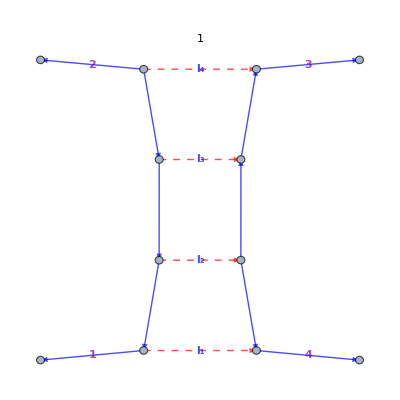
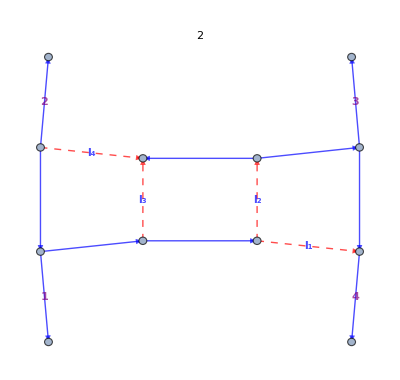
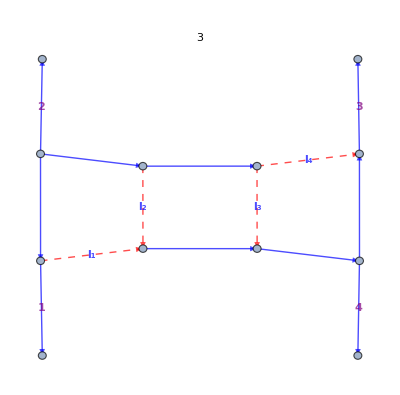
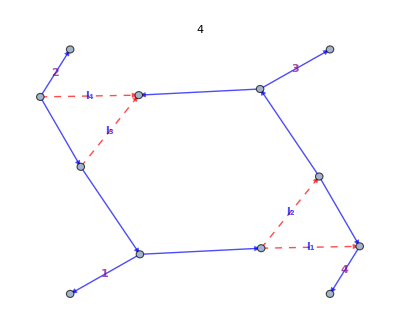
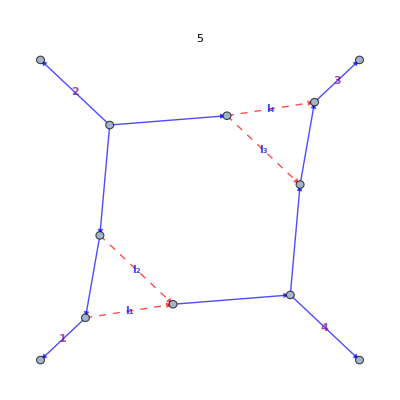
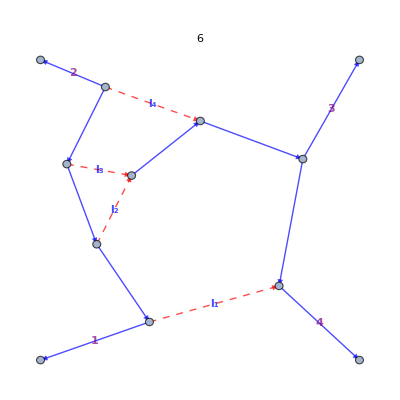
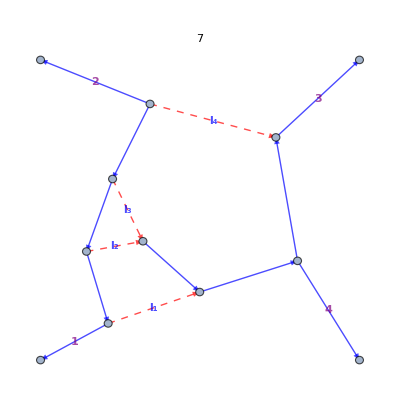
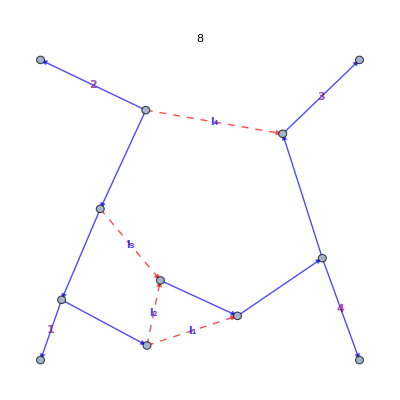
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
MapIndexed[(doOrderedPlot[#,k/@Range[4],PlotLabel->#2[[1]]]//cutDisplayRule)&,allCutGraphsT]
```

```mathematica
treesToLoops[allCutsT[[1]]]
```

```mathematica
Table[treesToLoops[allCutsT[[i]]],{i,1,3}]//Flatten
```

```mathematica
sp=ResourceFunction["SetPartitions"][{a,b,c}]
```

{{{a,b,c}},{{a},{b,c}},{{a,b},{c}},{{a,c},{b}},{{a},{b},{c}}}

```mathematica
sp[[1]]
```

{{a,b,c}}

```mathematica
aaaa=ResourceFunction["SetPartitions"][{Atree[{k[1],in[12],in[8]}],
Atree[{k[2],in[5],-in[12]}],
Atree[{-in[5],in[6],in[9]}],
Atree[{-in[6],in[7],in[10]}],
Atree[{-in[10],in[14],in[11]}],
Atree[{-in[11],-in[8],-in[9]}],
 Atree[{-in[7],in[13],k[3]}],
 Atree[{-in[14],-in[13],k[4]}]}]
```

```mathematica
Cut0[{Atree[{k[1],in[12],in[8]}],
Atree[{k[2],in[5],-in[12]}],
Atree[{-in[5],in[6],in[9]}],
Atree[{-in[6],in[7],in[10]}],
Atree[{-in[10],in[14],in[11]}],
Atree[{-in[11],-in[8],-in[9]}],
 Atree[{-in[7],in[13],k[3]}],
 Atree[{-in[14],-in[13],k[4]}]}]
```

```mathematica
aaa[[1]][[1]]//toGraph// doOrderedPlot[#,k/@Range[4]]&
```

-Graphics-

```mathematica
sewGraphs[(aaa[[2]][[1]]//treesToLoops)[[1]],(aaa[[2]][[2]]//treesToLoops)[[1]]]//doOrderedPlot[#,k/@Range[4]]&
```

-Graphics-

```mathematica
aaa[[2]]//Flatten//ToString//StringCount[#,"in[6]"]&
```

2

```mathematica
fancyFormatOff
```

```mathematica
aaa[[2]]//Flatten//ToString
```

5                                                                    5                      5
{Atree[{l[-], in[12], in[8]}], Atree[{k[2], in[5], -in[12]}], Atree[{-in[5], l[-], in[9]}], Atree[{-l[-], in[7], in[10]}], Atree[{-in[10], in[14], in[11]}], Atree[{-in[11], -in[8], -in[9]}], Atree[{-in[7], in[13], k[3]}], Atree[{-in[14], -in[13], k[4]}]}
          2                                                                    2                      2

```mathematica
Cut[a__,ini__]:=
Module[ {n=a//Flatten//ToString//StringCount[#,"ini"]&,
nnnn=a//Flatten//ToString//StringCount[#,"l["]&
},
(nnnn+2)/2;
c=If[EvenQ[n],l[(nnnn+2)/2],ini];

b=a/.{ini->c}
]
```

```mathematica
l[1]
```

```mathematica
l[1]
```

```mathematica
aaaa[[2]]
```

{{Atree[{k[1],in[12],in[8]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}}

```mathematica
aaaa[[1]]
```

{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}}

```mathematica
Cut[aaaa[[2]],in[5]]
```

{{Atree[{k[1],in[12],in[8]}]},{Atree[{k[2],l[1],-in[12]}],Atree[{-l[1],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}}

```mathematica
{{Atree[{k[1],in[12],in[8]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],k[1],in[9]}],Atree[{-k[1],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}}
```

{{Atree[{k[1],in[12],in[8]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],k[1],in[9]}],Atree[{-k[1],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}}

```mathematica
Cut1[aaaa[[2]]]
```

{{Atree[{k[1],l[8],l[4]}]},{Atree[{k[2],l[1],-l[8]}],Atree[{-l[1],l[2],l[5]}],Atree[{-l[2],l[3],l[6]}],Atree[{-l[6],l[10],l[7]}],Atree[{-l[7],-l[4],-l[5]}],Atree[{-l[3],l[9],k[3]}],Atree[{-l[10],-l[9],k[4]}]}}

```mathematica
aaaa[[2]]
```

{{Atree[{k[1],in[12],in[8]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}}

```mathematica
l/:in=.
k[1]/:l[1]=.
```

TagUnset::tagnf: 在 in 中未找到标签 l.

```mathematica
in[6]
```

in[6]

```mathematica
k[1]/:l[1]=.
```

TagUnset::sym: 位置 1 处的参数 k[1] 应该是一个符号.

k[1]/:l[1]=.

```mathematica
ClearAll[k,l,aaaa]
```

```mathematica
Clear[k[1]]
```

Clear::ssym: k[1] 不是一个符号或者一个字符串.

```mathematica
k[1]
```

k[1]

```mathematica
Cut1[a__]:=
Map[Cut[a,#]&,Table[in[i],{i,1,30}]]
```

```mathematica
Cut1[a__]:=
For[i = 0, i < 30, i++, a=Cut[a,in[i]]];
a
```

a

```mathematica
Cut1[a__]:=
Module[{},
For[i = 0, i < 30, i++, a=Cut[a,in[i]]];
a
]
```

```mathematica
Remove[in,l,k]
```

```mathematica
aaaa[[2]]
```

{{A_3^tree(k_1,in[12],in[8])},{A_3^tree(k_2,in[5],-in[12]),A_3^tree(-in[5],in[6],in[9]),A_3^tree(-in[6],in[7],in[10]),A_3^tree(-in[10],in[14],in[11]),A_3^tree(-in[11],-in[8],-in[9]),A_3^tree(-in[7],in[13],k_3),A_3^tree(-in[14],-in[13],k_4)}}

```mathematica
Sew[aaaa[[2]]]
```

First::normal: First[d] 中的位置 1 处应该是非原子表达式.

Last::normal: Last[d] 中的位置 1 处应该是非原子表达式.

MapThread::mptd: MapThread[Style[#1,#3]&,{graphPlotForm[First[d]],graphPlotForm[Last[d]],graphPlotForm[color]}] 中位置 {2, 1} 处的对象 graphPlotForm[First[d]] 只含有 0 个维度（要求维度为 1）.

GraphPlot::graph: 在 GraphPlot[MapThread[Style[#1,#3]&,{graphPlotForm[First[d]],graphPlotForm[Last[d]],graphPlotForm[color]}],DirectedEdges→True,Method→{Spri…ding},«1»,VertexCoordinateRules→{neckl[{-k_(«1»)}]→{-0.707107,-0.707107},neckl[{-k_(«1»)}]→{-0.707107,0.707107},neckl[{-k_(«1»)}]→{0.707107,0.707107},neckl[{-k_(«1»)}]→{0.707107,-0.707107}},EdgeRenderingFunction→(Flatten[{If[labelHash$202710[«1»]===l,{Dashed,Red,Arrowheads[«1»],Thick,Arrow[«1»]},If[SameQ[«2»],{«3»},{«4»}]]}]&)] 中 中位置 1 处应该是一个图对象.

GraphPlot[MapThread[Style[#1#2,#3]&,{graphPlotForm[First[d]],graphPlotForm[Last[d]],graphPlotForm[RGBColor[0, 0, 1]]}],DirectedEdges→True,Method→{SpringElectricalEmbedding},MultiedgeStyle→0.5,VertexCoordinateRules→{neckl[{-k_1}]→{-0.707107,-0.707107},neckl[{-k_2}]→{-0.707107,0.707107},neckl[{-k_3}]→{0.707107,0.707107},neckl[{-k_4}]→{0.707107,-0.707107}},EdgeRenderingFunction→(Flatten[{If[labelHash$202710[#3/.a_b_c_:>a->b]===l,{Dashed,Red,Arrowheads[{{0.05,0.75}}],Thick,Arrow[#1]},If[labelHash$202710[#3/.a_b_c_:>a->b]===highlight,{RGBColor[0.074189364461738, 0.5290608072022583, 0.0075379568169680325],Thick,Arrow[#1]},{Blue,Arrowheads[1/18],Thick,Arrow[#1]}]]}]&)]

```mathematica
sewGraphs[(aaaa[[2]][[1]]//treesToLoops)[[1]],(aaaa[[2]][[2]]//treesToLoops)[[1]]]
```

vertexFormGraph[{neckl[{k_1,in[12],in[8]}],neckl[{k_2,in[5],-in[12]}],neckl[{-in[5],in[6],in[9]}],neckl[{-in[6],in[7],in[10]}],neckl[{-in[10],in[14],in[11]}],neckl[{-in[11],-in[8],-in[9]}],neckl[{-in[7],in[13],k_3}],neckl[{-in[14],-in[13],k_4}]}]

```mathematica
Length[aaaa[[2]]]
```

```mathematica
Sew1[b]
```

First::normal: First[d] 中的位置 1 处应该是非原子表达式.

Last::normal: Last[d] 中的位置 1 处应该是非原子表达式.

MapThread::mptd: MapThread[Style[#1,#3]&,{graphPlotForm[First[d]],graphPlotForm[Last[d]],graphPlotForm[color]}] 中位置 {2, 1} 处的对象 graphPlotForm[First[d]] 只含有 0 个维度（要求维度为 1）.

GraphPlot::graph: 在 GraphPlot[MapThread[Style[#1,#3]&,{graphPlotForm[First[d]],graphPlotForm[Last[d]],graphPlotForm[color]}],«4»,EdgeRenderingFunction→(Flatten[{If[labelHash$244633[«1»]===l,{Dashed,Red,«10»[«1»],Thick,Arrow[«1»]},If[SameQ[«2»],{«3»},{«4»}]]}]&)] 中 中位置 1 处应该是一个图对象.

GraphPlot[MapThread[Style[#1#2,#3]&,{graphPlotForm[First[d]],graphPlotForm[Last[d]],graphPlotForm[RGBColor[0, 0, 1]]}],DirectedEdges→True,Method→{SpringElectricalEmbedding},MultiedgeStyle→0.5,VertexCoordinateRules→{neckl[{-k_1}]→{-0.707107,-0.707107},neckl[{-k_2}]→{-0.707107,0.707107},neckl[{-k_3}]→{0.707107,0.707107},neckl[{-k_4}]→{0.707107,-0.707107}},EdgeRenderingFunction→(Flatten[{If[labelHash$244633[#3/.a_b_c_:>a->b]===l,{Dashed,Red,Arrowheads[{{0.05,0.75}}],Thick,Arrow[#1]},If[labelHash$244633[#3/.a_b_c_:>a->b]===highlight,{RGBColor[0.074189364461738, 0.5290608072022583, 0.0075379568169680325],Thick,Arrow[#1]},{Blue,Arrowheads[1/18],Thick,Arrow[#1]}]]}]&)]

```mathematica
sewGraphs[(b[[1]]//treesToLoops)[[1]],(b[[1+1]]//treesToLoops)[[1]]]//First
```

{neckl[{k_1,in[12],in[8]}],neckl[{k_2,in[5],-in[12]}],neckl[{-in[5],in[6],in[9]}],neckl[{-in[6],in[7],in[10]}],neckl[{-in[10],in[14],in[11]}],neckl[{-in[11],-in[8],-in[9]}],neckl[{-in[7],in[13],k_3}],neckl[{-in[14],-in[13],k_4}]}

```mathematica
For[i = 0, i < Length[aaaa[[2]]]-1, i++, d=sewGraphs[(b[[i+1]]//treesToLoops)[[1]],(b[[i+2]]//treesToLoops)[[1]]]];
d//doOrderedPlot[#,k/@Range[4]]&
```

-Graphics-

```mathematica
d
```

d

```mathematica
c
```

```mathematica
aaaa//Length
```

```mathematica
aaaa[[1]][[1]]
```

{A_3^tree(k_1,in[12],in[8]),A_3^tree(k_2,in[5],-in[12]),A_3^tree(-in[5],in[6],in[9]),A_3^tree(-in[6],in[7],in[10]),A_3^tree(-in[10],in[14],in[11]),A_3^tree(-in[11],-in[8],-in[9]),A_3^tree(-in[7],in[13],k_3),A_3^tree(-in[14],-in[13],k_4)}

```mathematica
Sew3[aaaa[[200]]]
```

-Graphics-

```mathematica
SewTest1[aaaa]
```

$Aborted

```mathematica
bbbbb=Table[aaaa[[i]],{i,1,300}]
```

```mathematica
SewTest1[bbbbb]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
SewTest1[bbbbb][[1]]===SewTest1[bbbbb][[2]]
```

True

```mathematica
SewTest2[bbbbb]
```

{1,2,4,7,8,13,14,16,25,26,28,31,32,49,52,61,64,65,66,68,71,72,77,78,80,81,84,97,98}

```mathematica
SelectSew1[bbbbb]
```

{{{A_3^tree(k_1,in[12],in[8]),A_3^tree(k_2,in[5],-in[12]),A_3^tree(-in[5],in[6],in[9]),A_3^tree(-in[6],in[7],in[10]),A_3^tree(-in[10],in[14],in[11]),A_3^tree(-in[11],-in[8],-in[9]),A_3^tree(-in[7],in[13],k_3),A_3^tree(-in[14],-in[13],k_4)}},{{A_3^tree(k_1,in[12],in[8])},{A_3^tree(k_2,in[5],-in[12]),A_3^tree(-in[5],in[6],in[9]),A_3^tree(-in[6],in[7],in[10]),A_3^tree(-in[10],in[14],in[11]),A_3^tree(-in[11],-in[8],-in[9]),A_3^tree(-in[7],in[13],k_3),A_3^tree(-in[14],-in[13],k_4)}},{{A_3^tree(k_1,in[12],in[8]),A_3^tree(-in[5],in[6],in[9]),A_3^tree(-in[6],in[7],in[10]),A_3^tree(-in[10],in[14],in[11]),A_3^tree(-in[11],-in[8],-in[9]),A_3^tree(-in[7],in[13],k_3),A_3^tree(-in[14],-in[13],k_4)},{A_3^tree(k_2,in[5],-in[12])}},{{A_3^tree(k_1,in[12],in[8]),A_3^tree(k_2,in[5],-in[12]),A_3^tree(-in[6],in[7],in[10]),A_3^tree(-in[10],in[14],in[11]),A_3^tree(-in[11],-in[8],-in[9]),A_3^tree(-in[7],in[13],k_3),A_3^tree(-in[14],-in[13],k_4)},{A_3^tree(-in[5],in[6],in[9])}},{{A_3^tree(k_1,in[12],in[8]),A_3^tree(-in[5],in[6],in[9])},{A_3^tree(k_2,in[5],-in[12]),A_3^tree(-in[6],in[7],in[10]),A_3^tree(-in[10],in[14],in[11]),A_3^tree(-in[11],-in[8],-in[9]),A_3^tree(-in[7],in[13],k_3),A_3^tree(-in[14],-in[13],k_4)}}}

```mathematica
SelectSew1[bbbbb][[2]]
```

{{A_3^tree(k_1,in[12],in[8])},{A_3^tree(k_2,in[5],-in[12]),A_3^tree(-in[5],in[6],in[9]),A_3^tree(-in[6],in[7],in[10]),A_3^tree(-in[10],in[14],in[11]),A_3^tree(-in[11],-in[8],-in[9]),A_3^tree(-in[7],in[13],k_3),A_3^tree(-in[14],-in[13],k_4)}}

```mathematica
Cut2[SelectSew1[bbbbb][[2]][[1]],in[8]]
```

{Atree[{k[1],in[12],in[8]}]}

```mathematica
Cut3[SelectSew1[bbbbb][[2]][[1]]]
```

{Atree[{k[1],l[2],l[1]}]}

```mathematica
SelectSew1[bbbbb][[2]][[1]]
```

{Atree[{k[1],in[12],in[8]}]}

```mathematica
fancyFormatOff
```

```mathematica
If[OddQ[SelectSew1[bbbbb][[2]][[1]]//Flatten//ToString//StringCount[#,"in[8]"]&],l[(0+2)/2],in[8]]
```

```mathematica
c=l[1]
```

l[1]

```mathematica
SelectSew1[bbbbb][[2]][[1]]/.{in[8]->l[1]}
```

{Atree[{k[1],in[12],l[1]}]}

```mathematica
a=SelectSew1[bbbbb][[2]][[1]]
```

{Atree[{k[1],in[12],in[8]}]}

```mathematica
SelectSew1[bbbbb]
```

{{{Atree[{k[1],in[12],in[8]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}}}

```mathematica
bbbbb//SewTest2
```

{1}

```mathematica
Table[bbbbb[[i]][[j]],{i,1,Length[bbbbb]},{j,1,Length[bbbbb[[i]]]}]
```

{{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}]},{Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],in[5],-in[12]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}]},{Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-in[5],in[6],in[9]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[5],in[6],in[9]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}]},{Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}]}}}

```mathematica
Cut4[bbbbb]
```

{{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}]},{Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],in[5],-in[12]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}]},{Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-in[5],in[6],in[9]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[5],in[6],in[9]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}]},{Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}]}}}

```mathematica
bbbbb[[3]]//Length
```

2

```mathematica
bbbbb
```

{{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}]},{Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],in[5],-in[12]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}]},{Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-in[5],in[6],in[9]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[5],in[6],in[9]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}]},{Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}]}}}

```mathematica
Information[d$1413111]
```

```mathematica
bbbbb
```

{{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}]},{Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],in[5],-in[12]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}]},{Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-in[5],in[6],in[9]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[5],in[6],in[9]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}]},{Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}]}}}

```mathematica
eeeee[2][1]=(bbbbb//SelectSew1)[[2]][[1]]//Cut3
```

{Atree[{k[1],l[2],l[1]}]}

```mathematica
eeeee[2][1]
```

{Atree[{k[1],l[2],l[1]}]}

```mathematica
eeee[[1]][[1]]=0
```

Set::noval: 在部分赋值中的符号 eeee 没有立即值.

0

```mathematica
eeee
```

eeee

```mathematica
eeeeee=bbbbb
```

{{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}]},{Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],in[5],-in[12]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}]},{Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-in[5],in[6],in[9]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[5],in[6],in[9]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}]},{Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}]}}}

```mathematica
eeeeee[[1]][[1]]=1
```

1

```mathematica
(bbbbb//SelectSew1)===bbbbb
```

False

```mathematica
bbbbb//Cut4
```

{{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],in[5],-in[12]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-in[5],in[6],in[9]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[5],in[6],in[9]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}}}

```mathematica
((b//SelectSew1)[[2]][[1]])
```

```mathematica
bbbbb//Cut4
```

{{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],in[5],-in[12]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-in[5],in[6],in[9]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[5],in[6],in[9]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}}}

```mathematica
eeeeeee=bbbbb//SelectSew1
```

{{{Atree[{k[1],in[12],in[8]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}}}

```mathematica
c=Length[aaaa//SelectSew1]
```

```mathematica
bbbbb//SelectSew1
```

{{{Atree[{k[1],in[12],in[8]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}}}

```mathematica
dddd=Table[(bbbbb//SelectSew1)[[i]],{i,1,4}]
```

Part::partw: {{{Atree[{k[1],in[12],in[8]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],«1»,k[3]}],Atree[{-in[14],-in[13],k[4]}]}}} 的部分 80 不存在.

General::stop: 在本次计算中，Part::partw 的进一步输出将被抑制.

{{{{Atree[{k[1],in[12],in[8]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}}}⟦80⟧,{{{Atree[{k[1],in[12],in[8]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}}}⟦80⟧,{{{Atree[{k[1],in[12],in[8]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}}}⟦80⟧,{{{Atree[{k[1],in[12],in[8]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}}}⟦80⟧}

```mathematica
For[m = 0, m < c-1, m++,
For[n = 0, n < ((bbbbb//SelectSew1)[[m]])//Length-1, n++,
(eeeeeee)[[m]][[n]]=
((bbbbb//SelectSew1)[[m]][[n]])//Cut3
]
]
```

```mathematica
m
```

4

```mathematica
n
```

0

```mathematica
c
```

5

```mathematica
((bbbbb//SelectSew1)[[1]])//Length
```

1

```mathematica
((bbbbb//SelectSew1)[[2]][[1]])//Cut3
```

{Atree[{k[1],l[2],l[1]}]}

```mathematica
Cut4[bbbbb//SelectSew1][[2]][[1]]
```

{Atree[{k[1],l[2],l[1]}]}

```mathematica
bbbbbbb=Cut4[bbbbb]
```

{{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],l[2],l[1]}]},{Atree[{k[2],in[5],-l[2]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-l[1],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],l[2],in[8]}],Atree[{-l[1],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],l[1],-l[2]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],l[1],-in[12]}],Atree[{-l[2],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-l[3]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-l[1],l[2],l[3]}]}},{{Atree[{k[1],l[5],l[3]}],Atree[{-l[1],l[2],l[4]}]},{Atree[{k[2],l[1],-l[5]}],Atree[{-l[2],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-l[3],-l[4]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],l[1],in[9]}],Atree[{-l[3],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-l[2],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-l[1],l[2],l[3]}]}},{{Atree[{k[1],l[5],l[3]}],Atree[{-l[1],l[2],l[4]}]},{Atree[{k[2],in[5],-l[5]}],Atree[{-in[5],l[1],in[9]}],Atree[{-l[4],in[14],in[11]}],Atree[{-in[11],-l[3],-in[9]}],Atree[{-l[2],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],l[5],in[8]}],Atree[{-l[1],l[2],in[9]}],Atree[{-l[4],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-l[3],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],l[1],-l[5]}],Atree[{-l[2],l[3],l[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],l[1]}],Atree[{-l[2],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-l[3],-in[13],k[4]}]},{Atree[{-l[1],l[3],l[2]}]}},{{Atree[{k[1],l[4],l[1]}],Atree[{-l[2],l[5],l[3]}]},{Atree[{k[2],in[5],-l[4]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],l[2]}],Atree[{-l[3],-l[1],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-l[5],-in[13],k[4]}]}},{{Atree[{k[1],l[4],in[8]}],Atree[{-l[1],in[6],in[9]}],Atree[{-in[6],in[7],l[2]}],Atree[{-l[3],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-l[5],-in[13],k[4]}]},{Atree[{k[2],l[1],-l[4]}],Atree[{-l[2],l[5],l[3]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],l[1],-in[12]}],Atree[{-l[2],in[7],l[4]}],Atree[{-l[5],-in[8],-l[3]}],Atree[{-in[7],in[13],k[3]}],Atree[{-l[6],-in[13],k[4]}]},{Atree[{-l[1],l[2],l[3]}],Atree[{-l[4],l[6],l[5]}]}},{{Atree[{k[1],l[7],l[3]}],Atree[{-l[1],l[2],l[4]}],Atree[{-l[5],l[8],l[6]}]},{Atree[{k[2],l[1],-l[7]}],Atree[{-l[2],in[7],l[5]}],Atree[{-l[6],-l[3],-l[4]}],Atree[{-in[7],in[13],k[3]}],Atree[{-l[8],-in[13],k[4]}]}},{{Atree[{k[1],in[12],l[1]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],l[2]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],l[3]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-l[3],-l[1],-l[2]}]}},{{Atree[{k[1],l[5],l[2]}],Atree[{-l[1],in[6],l[3]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],l[4]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],l[1],-l[5]}],Atree[{-l[4],-l[2],-l[3]}]}},{{Atree[{k[1],in[12],l[3]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],l[1],l[4]}],Atree[{-l[5],in[14],l[6]}],Atree[{-l[2],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-l[1],l[2],l[5]}],Atree[{-l[6],-l[3],-l[4]}]}},{{Atree[{k[1],l[8],l[4]}],Atree[{-l[1],l[2],l[5]}],Atree[{-l[6],in[14],l[7]}],Atree[{-l[3],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],l[1],-l[8]}],Atree[{-l[2],l[3],l[6]}],Atree[{-l[7],-l[4],-l[5]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],l[2],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],l[1],k[3]}]},{Atree[{-l[2],-l[1],k[4]}]}},{{Atree[{k[1],l[2],l[1]}],Atree[{-l[4],-l[3],k[4]}]},{Atree[{k[2],in[5],-l[2]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],l[4],in[11]}],Atree[{-in[11],-l[1],-in[9]}],Atree[{-in[7],l[3],k[3]}]}},{{Atree[{k[1],l[2],in[8]}],Atree[{-l[1],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],l[4],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],l[3],k[3]}]},{Atree[{k[2],l[1],-l[2]}],Atree[{-l[4],-l[3],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],l[1],-in[12]}],Atree[{-l[2],in[7],in[10]}],Atree[{-in[10],l[5],in[11]}],Atree[{-in[11],-in[8],-l[3]}],Atree[{-in[7],l[4],k[3]}]},{Atree[{-l[1],l[2],l[3]}],Atree[{-l[5],-l[4],k[4]}]}},{{Atree[{k[1],l[5],l[3]}],Atree[{-l[1],l[2],l[4]}],Atree[{-l[7],-l[6],k[4]}]},{Atree[{k[2],l[1],-l[5]}],Atree[{-l[2],in[7],in[10]}],Atree[{-in[10],l[7],in[11]}],Atree[{-in[11],-l[3],-l[4]}],Atree[{-in[7],l[6],k[3]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],l[1],in[9]}],Atree[{-l[3],l[5],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-l[2],l[4],k[3]}]},{Atree[{-l[1],l[2],l[3]}],Atree[{-l[5],-l[4],k[4]}]}},{{Atree[{k[1],l[5],l[3]}],Atree[{-l[1],l[2],l[4]}],Atree[{-l[7],-l[6],k[4]}]},{Atree[{k[2],in[5],-l[5]}],Atree[{-in[5],l[1],in[9]}],Atree[{-l[4],l[7],in[11]}],Atree[{-in[11],-l[3],-in[9]}],Atree[{-l[2],l[6],k[3]}]}},{{Atree[{k[1],l[5],in[8]}],Atree[{-l[1],l[2],in[9]}],Atree[{-l[4],l[7],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-l[3],l[6],k[3]}]},{Atree[{k[2],l[1],-l[5]}],Atree[{-l[2],l[3],l[4]}],Atree[{-l[7],-l[6],k[4]}]}},{{Atree[{k[1],in[12],l[2]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],l[3]}],Atree[{-in[6],l[1],in[10]}],Atree[{-in[10],in[14],l[4]}],Atree[{-in[14],-l[5],k[4]}]},{Atree[{-l[4],-l[2],-l[3]}],Atree[{-l[1],l[5],k[3]}]}},{{Atree[{k[1],l[6],l[3]}],Atree[{-l[1],in[6],l[4]}],Atree[{-in[6],l[2],in[10]}],Atree[{-in[10],in[14],l[5]}],Atree[{-in[14],-l[7],k[4]}]},{Atree[{k[2],l[1],-l[6]}],Atree[{-l[5],-l[3],-l[4]}],Atree[{-l[2],l[7],k[3]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],l[1],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[14],-l[2],k[4]}]},{Atree[{-l[1],l[2],k[3]}]}},{{Atree[{k[1],l[3],l[2]}],Atree[{-l[1],l[4],k[3]}]},{Atree[{k[2],in[5],-l[3]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],l[1],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-l[2],-in[9]}],Atree[{-in[14],-l[4],k[4]}]}},{{Atree[{k[1],l[3],in[8]}],Atree[{-l[1],in[6],in[9]}],Atree[{-in[6],l[2],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[14],-l[4],k[4]}]},{Atree[{k[2],l[1],-l[3]}],Atree[{-l[2],l[4],k[3]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],l[1],-in[12]}],Atree[{-l[2],l[3],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-l[4]}],Atree[{-in[14],-l[5],k[4]}]},{Atree[{-l[1],l[2],l[4]}],Atree[{-l[3],l[5],k[3]}]}},{{Atree[{k[1],l[6],l[4]}],Atree[{-l[1],l[2],l[5]}],Atree[{-l[3],l[7],k[3]}]},{Atree[{k[2],l[1],-l[6]}],Atree[{-l[2],l[3],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-l[4],-l[5]}],Atree[{-in[14],-l[7],k[4]}]}},{{Atree[{k[1],in[12],l[1]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],l[2]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],l[5],l[3]}],Atree[{-in[7],l[4],k[3]}]},{Atree[{-l[3],-l[1],-l[2]}],Atree[{-l[5],-l[4],k[4]}]}},{{Atree[{k[1],l[5],l[2]}],Atree[{-l[1],in[6],l[3]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],l[7],l[4]}],Atree[{-in[7],l[6],k[3]}]},{Atree[{k[2],l[1],-l[5]}],Atree[{-l[4],-l[2],-l[3]}],Atree[{-l[7],-l[6],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],l[1],l[2]}],Atree[{-l[3],-in[8],-in[9]}],Atree[{-l[5],-l[4],k[4]}]},{Atree[{-l[2],l[5],l[3]}],Atree[{-l[1],l[4],k[3]}]}},{{Atree[{k[1],l[5],l[2]}],Atree[{-l[3],l[7],l[4]}],Atree[{-l[1],l[6],k[3]}]},{Atree[{k[2],in[5],-l[5]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],l[1],l[3]}],Atree[{-l[4],-l[2],-in[9]}],Atree[{-l[7],-l[6],k[4]}]}},{{Atree[{k[1],l[5],in[8]}],Atree[{-l[1],in[6],in[9]}],Atree[{-in[6],l[2],l[3]}],Atree[{-l[4],-in[8],-in[9]}],Atree[{-l[7],-l[6],k[4]}]},{Atree[{k[2],l[1],-l[5]}],Atree[{-l[3],l[7],l[4]}],Atree[{-l[2],l[6],k[3]}]}},{{Atree[{k[1],in[12],l[3]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],l[1],l[4]}],Atree[{-l[5],l[8],l[6]}],Atree[{-l[2],l[7],k[3]}]},{Atree[{-l[1],l[2],l[5]}],Atree[{-l[6],-l[3],-l[4]}],Atree[{-l[8],-l[7],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],l[1],-in[12]}],Atree[{-l[2],l[3],l[5]}],Atree[{-l[6],-in[8],-l[4]}],Atree[{-l[8],-l[7],k[4]}]},{Atree[{-l[1],l[2],l[4]}],Atree[{-l[5],l[8],l[6]}],Atree[{-l[3],l[7],k[3]}]}},{{Atree[{k[1],l[8],l[4]}],Atree[{-l[1],l[2],l[5]}],Atree[{-l[6],l[10],l[7]}],Atree[{-l[3],l[9],k[3]}]},{Atree[{k[2],l[1],-l[8]}],Atree[{-l[2],l[3],l[6]}],Atree[{-l[7],-l[4],-l[5]}],Atree[{-l[10],-l[9],k[4]}]}},{{Atree[{k[1],l[2],l[1]}]},{Atree[{k[2],l[1],-l[5]}],Atree[{-l[2],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-l[3],-l[4]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-l[1],l[2],l[3]}]}},{{Atree[{k[1],l[2],l[1]}]},{Atree[{k[2],in[5],-l[5]}],Atree[{-in[5],l[1],in[9]}],Atree[{-l[4],in[14],in[11]}],Atree[{-in[11],-l[3],-in[9]}],Atree[{-l[2],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-l[1],l[2],l[3]}]}},{{Atree[{k[1],l[2],l[1]}]},{Atree[{k[2],in[5],-l[4]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],l[2]}],Atree[{-l[3],-l[1],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-l[5],-in[13],k[4]}]},{Atree[{-l[1],l[3],l[2]}]}},{{Atree[{k[1],l[2],l[1]}]},{Atree[{k[2],l[1],-l[7]}],Atree[{-l[2],in[7],l[5]}],Atree[{-l[6],-l[3],-l[4]}],Atree[{-in[7],in[13],k[3]}],Atree[{-l[8],-in[13],k[4]}]},{Atree[{-l[1],l[2],l[3]}],Atree[{-l[4],l[6],l[5]}]}},{{Atree[{k[1],l[2],l[1]}]},{Atree[{k[2],in[5],-l[3]}],Atree[{-in[5],in[6],l[1]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],l[2]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-l[3],-l[1],-l[2]}]}},{{Atree[{k[1],l[2],l[1]}]},{Atree[{k[2],in[5],-l[6]}],Atree[{-in[5],l[1],l[3]}],Atree[{-l[4],in[14],l[5]}],Atree[{-l[2],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-l[1],l[2],l[5]}],Atree[{-l[6],-l[3],-l[4]}]}},{{Atree[{k[1],l[2],l[1]}]},{Atree[{k[2],in[5],-l[2]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],l[4],in[11]}],Atree[{-in[11],-l[1],-in[9]}],Atree[{-in[7],l[3],k[3]}]},{Atree[{-l[2],-l[1],k[4]}]}},{{Atree[{k[1],l[2],l[1]}]},{Atree[{k[2],l[1],-l[5]}],Atree[{-l[2],in[7],in[10]}],Atree[{-in[10],l[7],in[11]}],Atree[{-in[11],-l[3],-l[4]}],Atree[{-in[7],l[6],k[3]}]},{Atree[{-l[1],l[2],l[3]}],Atree[{-l[5],-l[4],k[4]}]}},{{Atree[{k[1],l[2],l[1]}]},{Atree[{k[2],in[5],-l[5]}],Atree[{-in[5],l[1],in[9]}],Atree[{-l[4],l[7],in[11]}],Atree[{-in[11],-l[3],-in[9]}],Atree[{-l[2],l[6],k[3]}]},{Atree[{-l[1],l[2],l[3]}],Atree[{-l[5],-l[4],k[4]}]}},{{Atree[{k[1],l[2],l[1]}]},{Atree[{k[2],in[5],-l[4]}],Atree[{-in[5],in[6],l[2]}],Atree[{-in[6],l[1],in[10]}],Atree[{-in[10],in[14],l[3]}],Atree[{-in[14],-l[5],k[4]}]},{Atree[{-l[4],-l[2],-l[3]}],Atree[{-l[1],l[5],k[3]}]}},{{Atree[{k[1],l[2],l[1]}]},{Atree[{k[2],in[5],-l[3]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],l[1],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-l[2],-in[9]}],Atree[{-in[14],-l[4],k[4]}]},{Atree[{-l[1],l[2],k[3]}]}},{{Atree[{k[1],l[2],l[1]}]},{Atree[{k[2],l[1],-l[6]}],Atree[{-l[2],l[3],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-l[4],-l[5]}],Atree[{-in[14],-l[7],k[4]}]},{Atree[{-l[1],l[2],l[4]}],Atree[{-l[3],l[5],k[3]}]}},{{Atree[{k[1],l[2],l[1]}]},{Atree[{k[2],in[5],-l[3]}],Atree[{-in[5],in[6],l[1]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],l[5],l[2]}],Atree[{-in[7],l[4],k[3]}]},{Atree[{-l[3],-l[1],-l[2]}],Atree[{-l[5],-l[4],k[4]}]}},{{Atree[{k[1],l[2],l[1]}]},{Atree[{k[2],in[5],-l[5]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],l[1],l[3]}],Atree[{-l[4],-l[2],-in[9]}],Atree[{-l[7],-l[6],k[4]}]},{Atree[{-l[2],l[5],l[3]}],Atree[{-l[1],l[4],k[3]}]}},{{Atree[{k[1],l[2],l[1]}]},{Atree[{k[2],in[5],-l[6]}],Atree[{-in[5],l[1],l[3]}],Atree[{-l[4],l[8],l[5]}],Atree[{-l[2],l[7],k[3]}]},{Atree[{-l[1],l[2],l[5]}],Atree[{-l[6],-l[3],-l[4]}],Atree[{-l[8],-l[7],k[4]}]}},{{Atree[{k[1],l[2],l[1]}]},{Atree[{k[2],l[1],-l[8]}],Atree[{-l[2],l[3],l[6]}],Atree[{-l[7],-l[4],-l[5]}],Atree[{-l[10],-l[9],k[4]}]},{Atree[{-l[1],l[2],l[4]}],Atree[{-l[5],l[8],l[6]}],Atree[{-l[3],l[7],k[3]}]}},{{Atree[{k[1],l[3],in[8]}],Atree[{-l[1],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-l[2]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],l[1],-l[2]}]},{Atree[{-l[1],l[2],l[3]}]}},{{Atree[{k[1],l[5],in[8]}],Atree[{-l[1],l[2],in[9]}],Atree[{-l[4],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-l[3],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],l[1],-l[2]}]},{Atree[{-l[1],l[2],l[3]}]}},{{Atree[{k[1],l[4],in[8]}],Atree[{-l[1],in[6],in[9]}],Atree[{-in[6],in[7],l[2]}],Atree[{-l[3],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-l[5],-in[13],k[4]}]},{Atree[{k[2],l[1],-l[2]}]},{Atree[{-l[1],l[3],l[2]}]}},{{Atree[{k[1],l[5],in[8]}],Atree[{-l[1],in[7],l[3]}],Atree[{-l[4],-in[8],-l[2]}],Atree[{-in[7],in[13],k[3]}],Atree[{-l[6],-in[13],k[4]}]},{Atree[{k[2],l[1],-l[2]}]},{Atree[{-l[1],l[2],l[3]}],Atree[{-l[4],l[6],l[5]}]}},{{Atree[{k[1],l[5],l[2]}],Atree[{-l[1],in[6],l[3]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],l[4]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],l[1],-l[2]}]},{Atree[{-l[3],-l[1],-l[2]}]}},{{Atree[{k[1],l[8],l[4]}],Atree[{-l[1],l[2],l[5]}],Atree[{-l[6],in[14],l[7]}],Atree[{-l[3],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],l[1],-l[2]}]},{Atree[{-l[1],l[2],l[5]}],Atree[{-l[6],-l[3],-l[4]}]}},{{Atree[{k[1],l[2],in[8]}],Atree[{-l[1],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],l[4],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],l[3],k[3]}]},{Atree[{k[2],l[1],-l[2]}]},{Atree[{-l[2],-l[1],k[4]}]}},{{Atree[{k[1],l[3],in[8]}],Atree[{-l[1],in[7],in[10]}],Atree[{-in[10],l[5],in[11]}],Atree[{-in[11],-in[8],-l[2]}],Atree[{-in[7],l[4],k[3]}]},{Atree[{k[2],l[1],-l[2]}]},{Atree[{-l[1],l[2],l[3]}],Atree[{-l[5],-l[4],k[4]}]}},{{Atree[{k[1],l[5],in[8]}],Atree[{-l[1],l[2],in[9]}],Atree[{-l[4],l[7],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-l[3],l[6],k[3]}]},{Atree[{k[2],l[1],-l[2]}]},{Atree[{-l[1],l[2],l[3]}],Atree[{-l[5],-l[4],k[4]}]}},{{Atree[{k[1],l[6],l[3]}],Atree[{-l[1],in[6],l[4]}],Atree[{-in[6],l[2],in[10]}],Atree[{-in[10],in[14],l[5]}],Atree[{-in[14],-l[7],k[4]}]},{Atree[{k[2],l[1],-l[2]}]},{Atree[{-l[4],-l[2],-l[3]}],Atree[{-l[1],l[5],k[3]}]}},{{Atree[{k[1],l[3],in[8]}],Atree[{-l[1],in[6],in[9]}],Atree[{-in[6],l[2],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[14],-l[4],k[4]}]},{Atree[{k[2],l[1],-l[2]}]},{Atree[{-l[1],l[2],k[3]}]}},{{Atree[{k[1],l[4],in[8]}],Atree[{-l[1],l[2],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-l[3]}],Atree[{-in[14],-l[5],k[4]}]},{Atree[{k[2],l[1],-l[2]}]},{Atree[{-l[1],l[2],l[4]}],Atree[{-l[3],l[5],k[3]}]}},{{Atree[{k[1],l[5],l[2]}],Atree[{-l[1],in[6],l[3]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],l[7],l[4]}],Atree[{-in[7],l[6],k[3]}]},{Atree[{k[2],l[1],-l[2]}]},{Atree[{-l[3],-l[1],-l[2]}],Atree[{-l[5],-l[4],k[4]}]}},{{Atree[{k[1],l[5],in[8]}],Atree[{-l[1],in[6],in[9]}],Atree[{-in[6],l[2],l[3]}],Atree[{-l[4],-in[8],-in[9]}],Atree[{-l[7],-l[6],k[4]}]},{Atree[{k[2],l[1],-l[2]}]},{Atree[{-l[2],l[5],l[3]}],Atree[{-l[1],l[4],k[3]}]}},{{Atree[{k[1],in[12],l[2]}],Atree[{k[2],l[1],-in[12]}]},{Atree[{-l[1],l[2],l[4]}],Atree[{-l[5],l[8],l[6]}],Atree[{-l[3],l[7],k[3]}]},{Atree[{-l[1],l[2],l[5]}],Atree[{-l[6],-l[3],-l[4]}],Atree[{-l[8],-l[7],k[4]}]}},{{Atree[{k[1],l[8],l[4]}],Atree[{-l[1],l[2],l[5]}],Atree[{-l[6],l[10],l[7]}],Atree[{-l[3],l[9],k[3]}]},{Atree[{k[2],l[1],-l[2]}]},{Atree[{-l[1],l[2],l[5]}],Atree[{-l[6],-l[3],-l[4]}],Atree[{-l[8],-l[7],k[4]}]}},{{Atree[{k[1],l[6],in[8]}],Atree[{-l[1],l[2],l[4]}],Atree[{-l[5],-in[8],-l[3]}],Atree[{-l[8],-l[7],k[4]}]},{Atree[{k[2],l[1],-l[2]}]},{Atree[{-l[1],l[2],l[4]}],Atree[{-l[5],l[8],l[6]}],Atree[{-l[3],l[7],k[3]}]}},{{Atree[{k[1],l[4],in[8]}],Atree[{-l[3],in[14],in[11]}],Atree[{-in[11],-in[8],-l[2]}],Atree[{-l[1],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],l[1],-l[5]}],Atree[{-l[2],l[3],l[4]}]},{Atree[{-l[1],l[2],l[3]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],l[1],-in[12]}],Atree[{-l[4],in[14],in[11]}],Atree[{-in[11],-in[8],-l[3]}],Atree[{-l[2],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-l[1],l[2],l[3]}]},{Atree[{-l[1],l[2],l[3]}]}},{{Atree[{k[1],l[5],l[3]}],Atree[{-l[1],l[2],l[4]}]},{Atree[{k[2],l[1],-l[6]}],Atree[{-l[5],in[14],in[11]}],Atree[{-in[11],-l[3],-l[4]}],Atree[{-l[2],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-l[1],l[2],l[3]}]}},{{Atree[{k[1],l[5],l[3]}],Atree[{-l[1],l[2],l[4]}]},{Atree[{k[2],l[1],-l[6]}],Atree[{-l[5],in[14],in[11]}],Atree[{-in[11],-l[3],-l[4]}],Atree[{-l[2],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-l[1],l[2],l[3]}]}}}

```mathematica
leftTreeGraphs[[1]]
```

vertexFormGraph[{neckl[{in[1],k[2],l[3]}],neckl[{-in[1],l[2],in[2]}],neckl[{-in[2],l[1],k[1]}]}]

```mathematica
bbbbbbb[[2]][[2]]
```

{Atree[{k[2],in[5],-l[2]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-l[1],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}

```mathematica
bbbbbbb[[2]][[2]]//SewSew1
```

vertexFormGraph[{neckl[{k[2],in[5],-l[2]}],neckl[{-in[5],in[6],in[9]}],neckl[{-in[6],in[7],in[10]}],neckl[{-in[10],in[14],in[11]}],neckl[{-in[11],-l[1],-in[9]}],neckl[{-in[7],in[13],k[3]}],neckl[{-in[14],-in[13],k[4]}]}]

```mathematica
sewGraphs[bbbbbbb[[4]][[1]]//SewSew1,bbbbbbb[[4]][[2]]//SewSew1]//doOrderedPlot[#,k/@Range[4]]&
```

-Graphics-

```mathematica
cccc=UncutOff[bbbbb]
```

{{{Atree[{k[1],in[12],in[8]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}]},{Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],in[5],-in[12]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}]},{Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-in[5],in[6],in[9]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[5],in[6],in[9]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}]},{Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}]}}}

```mathematica
SewTest2[bbbbb]
```

{1}

```mathematica
bbbbb
```

```mathematica
(bbbbb//SelectSew3)[[50]]//Length
```

```mathematica
bbbbb//Cut4//SelectSew4
```

{}

```mathematica
ccccc[[2]][[1]]
```

vertexFormGraph[{neckl[{k[1],in[12],in[8]}],neckl[{-in[5],in[6],in[9]}],neckl[{-in[6],in[7],in[10]}],neckl[{-in[10],in[14],in[11]}],neckl[{-in[11],-in[8],-in[9]}],neckl[{-in[7],in[13],k[3]}],neckl[{-in[14],-in[13],k[4]}]}]

```mathematica
sewGraphs[ccccc[[2]][[1]],ccccc[[2]][[2]]]//doOrderedPlot[#,k/@Range[4]]&
```

-Graphics-

```mathematica
bbbbb[[2]][[1]]
```

{Atree[{k[1],in[12],in[8]}]}

```mathematica
bbbbbbb[[2]][[1]]
```

{Atree[{k[1],l[2],l[1]}]}

```mathematica
bbbbb//SelectSew4
```

```mathematica
bbbbbbb//SelectSew1
```

CanonicalGraph::graph: 在 CanonicalGraph[Graph[graphPlotForm[{{Directive[Opacity[0.7],color],{Style[{«4»},RGBColor[«3»]],Text[k[«1»],{«2»},ImageScaled[«1»],UndirectedEdge[«2»]]},«8»,«5»},{Directive[color,EdgeForm[Directive[«2»]]],«9»,«3»}}]]] 中 中位置 1 处应该是一个图对象.

CanonicalGraph::graph: 在 CanonicalGraph[Graph[graphPlotForm[{{Directive[Opacity[0.7],color],{Style[{«5»},{«2»}],Text[l[«1»],{«2»},ImageScaled[«1»],UndirectedEdge[«2»]]},«8»,«5»},{Directive[color,EdgeForm[Directive[«2»]]],«9»,«3»}}]]] 中 中位置 1 处应该是一个图对象.

General::stop: 在本次计算中，CanonicalGraph::graph 的进一步输出将被抑制.

{{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}}}

```mathematica
isIsomorphic[SewTest1[bbbbbbb][[2]],SewTest1[bbbbbbb][[1]]]
```

False

```mathematica
SewTest3[bbbbb]
```

{{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],in[5],-in[12]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-in[5],in[6],in[9]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[5],in[6],in[9]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-in[6],in[7],in[10]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[6],in[7],in[10]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[6],in[7],in[10]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-in[10],in[14],in[11]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[10],in[14],in[11]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[10],in[14],in[11]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-in[5],in[6],in[9]}],Atree[{-in[10],in[14],in[11]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[10],in[14],in[11]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-in[11],-in[8],-in[9]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[11],-in[8],-in[9]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-in[6],in[7],in[10]}],Atree[{-in[11],-in[8],-in[9]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[11],-in[8],-in[9]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}]},{Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}]},{Atree[{-in[5],in[6],in[9]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}]},{Atree[{-in[6],in[7],in[10]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-in[7],in[13],k[3]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[7],in[13],k[3]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[7],in[13],k[3]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-in[5],in[6],in[9]}],Atree[{-in[7],in[13],k[3]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[7],in[13],k[3]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[7],in[13],k[3]}]},{Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[7],in[13],k[3]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-in[10],in[14],in[11]}],Atree[{-in[7],in[13],k[3]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[7],in[13],k[3]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[7],in[13],k[3]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[7],in[13],k[3]}]},{Atree[{-in[6],in[7],in[10]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-in[5],in[6],in[9]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[7],in[13],k[3]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[7],in[13],k[3]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-in[5],in[6],in[9]}]}},{{Atree[{k[1],in[12],in[8]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-in[6],in[7],in[10]}]}},{{Atree[{k[1],in[12],in[8]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-in[10],in[14],in[11]}]}},{{Atree[{k[1],in[12],in[8]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-in[5],in[6],in[9]}],Atree[{-in[10],in[14],in[11]}]}},{{Atree[{k[1],in[12],in[8]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-in[11],-in[8],-in[9]}]}},{{Atree[{k[1],in[12],in[8]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-in[6],in[7],in[10]}],Atree[{-in[11],-in[8],-in[9]}]}},{{Atree[{k[1],in[12],in[8]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}]},{Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}]},{Atree[{-in[5],in[6],in[9]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}]},{Atree[{-in[6],in[7],in[10]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}]}},{{Atree[{k[1],in[12],in[8]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-in[7],in[13],k[3]}]}},{{Atree[{k[1],in[12],in[8]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-in[5],in[6],in[9]}],Atree[{-in[7],in[13],k[3]}]}},{{Atree[{k[1],in[12],in[8]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[7],in[13],k[3]}]},{Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-in[10],in[14],in[11]}],Atree[{-in[7],in[13],k[3]}]}},{{Atree[{k[1],in[12],in[8]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[7],in[13],k[3]}]},{Atree[{-in[6],in[7],in[10]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-in[5],in[6],in[9]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[7],in[13],k[3]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],in[5],-in[12]}]},{Atree[{-in[5],in[6],in[9]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],in[5],-in[12]}]},{Atree[{-in[6],in[7],in[10]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],in[5],-in[12]}]},{Atree[{-in[10],in[14],in[11]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],in[5],-in[12]}]},{Atree[{-in[5],in[6],in[9]}],Atree[{-in[10],in[14],in[11]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],in[5],-in[12]}]},{Atree[{-in[11],-in[8],-in[9]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],in[5],-in[12]}]},{Atree[{-in[6],in[7],in[10]}],Atree[{-in[11],-in[8],-in[9]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}]},{Atree[{k[2],in[5],-in[12]}]},{Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}]},{Atree[{k[2],in[5],-in[12]}]},{Atree[{-in[5],in[6],in[9]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}]},{Atree[{k[2],in[5],-in[12]}]},{Atree[{-in[6],in[7],in[10]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],in[5],-in[12]}]},{Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],in[5],-in[12]}]},{Atree[{-in[7],in[13],k[3]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],in[5],-in[12]}]},{Atree[{-in[5],in[6],in[9]}],Atree[{-in[7],in[13],k[3]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[7],in[13],k[3]}]},{Atree[{k[2],in[5],-in[12]}]},{Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],in[5],-in[12]}]},{Atree[{-in[10],in[14],in[11]}],Atree[{-in[7],in[13],k[3]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}]},{Atree[{-in[5],in[6],in[9]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[7],in[13],k[3]}]},{Atree[{-in[6],in[7],in[10]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[7],in[13],k[3]}]},{Atree[{k[2],in[5],-in[12]}]},{Atree[{-in[6],in[7],in[10]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],in[5],-in[12]}]},{Atree[{-in[5],in[6],in[9]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[7],in[13],k[3]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[6],in[7],in[10]}]},{Atree[{-in[5],in[6],in[9]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-in[5],in[6],in[9]}]},{Atree[{-in[6],in[7],in[10]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[5],in[6],in[9]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-in[6],in[7],in[10]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{-in[6],in[7],in[10]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-in[5],in[6],in[9]}]}}}

```mathematica
SewTest4[bbbbb]
```

Part::partw: {{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[«1»],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}},«9»,«67»} 的部分 78 不存在.

Part::partw: {{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[«1»],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}},«9»,«67»} 的部分 80 不存在.

Part::partw: {{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[«1»],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}},«9»,«67»} 的部分 81 不存在.

General::stop: 在本次计算中，Part::partw 的进一步输出将被抑制.

```mathematica
Length[bbbbbbb]
```

77

```mathematica
bbbbb//SelectSew3
```

{{{Atree[{k[1],l[2],l[1]}]},{Atree[{k[2],in[5],-l[2]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-l[1],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],l[2],in[8]}],Atree[{-l[1],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],l[1],-l[2]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],l[1],-in[12]}],Atree[{-l[2],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-l[3]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-l[1],l[2],l[3]}]}},{{Atree[{k[1],l[5],l[3]}],Atree[{-l[1],l[2],l[4]}]},{Atree[{k[2],l[1],-l[5]}],Atree[{-l[2],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-l[3],-l[4]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],l[1],in[9]}],Atree[{-l[3],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-l[2],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-l[1],l[2],l[3]}]}},{{Atree[{k[1],l[5],l[3]}],Atree[{-l[1],l[2],l[4]}]},{Atree[{k[2],in[5],-l[5]}],Atree[{-in[5],l[1],in[9]}],Atree[{-l[4],in[14],in[11]}],Atree[{-in[11],-l[3],-in[9]}],Atree[{-l[2],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],l[5],in[8]}],Atree[{-l[1],l[2],in[9]}],Atree[{-l[4],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-l[3],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],l[1],-l[5]}],Atree[{-l[2],l[3],l[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],l[1]}],Atree[{-l[2],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-l[3],-in[13],k[4]}]},{Atree[{-l[1],l[3],l[2]}]}},{{Atree[{k[1],l[4],l[1]}],Atree[{-l[2],l[5],l[3]}]},{Atree[{k[2],in[5],-l[4]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],l[2]}],Atree[{-l[3],-l[1],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-l[5],-in[13],k[4]}]}},{{Atree[{k[1],l[4],in[8]}],Atree[{-l[1],in[6],in[9]}],Atree[{-in[6],in[7],l[2]}],Atree[{-l[3],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-l[5],-in[13],k[4]}]},{Atree[{k[2],l[1],-l[4]}],Atree[{-l[2],l[5],l[3]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],l[1],-in[12]}],Atree[{-l[2],in[7],l[4]}],Atree[{-l[5],-in[8],-l[3]}],Atree[{-in[7],in[13],k[3]}],Atree[{-l[6],-in[13],k[4]}]},{Atree[{-l[1],l[2],l[3]}],Atree[{-l[4],l[6],l[5]}]}},{{Atree[{k[1],l[7],l[3]}],Atree[{-l[1],l[2],l[4]}],Atree[{-l[5],l[8],l[6]}]},{Atree[{k[2],l[1],-l[7]}],Atree[{-l[2],in[7],l[5]}],Atree[{-l[6],-l[3],-l[4]}],Atree[{-in[7],in[13],k[3]}],Atree[{-l[8],-in[13],k[4]}]}},{{Atree[{k[1],in[12],l[1]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],l[2]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],l[3]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-l[3],-l[1],-l[2]}]}},{{Atree[{k[1],l[5],l[2]}],Atree[{-l[1],in[6],l[3]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],l[4]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],l[1],-l[5]}],Atree[{-l[4],-l[2],-l[3]}]}},{{Atree[{k[1],in[12],l[3]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],l[1],l[4]}],Atree[{-l[5],in[14],l[6]}],Atree[{-l[2],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-l[1],l[2],l[5]}],Atree[{-l[6],-l[3],-l[4]}]}},{{Atree[{k[1],l[8],l[4]}],Atree[{-l[1],l[2],l[5]}],Atree[{-l[6],in[14],l[7]}],Atree[{-l[3],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],l[1],-l[8]}],Atree[{-l[2],l[3],l[6]}],Atree[{-l[7],-l[4],-l[5]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],l[2],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],l[1],k[3]}]},{Atree[{-l[2],-l[1],k[4]}]}},{{Atree[{k[1],l[2],l[1]}],Atree[{-l[4],-l[3],k[4]}]},{Atree[{k[2],in[5],-l[2]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],l[4],in[11]}],Atree[{-in[11],-l[1],-in[9]}],Atree[{-in[7],l[3],k[3]}]}},{{Atree[{k[1],l[2],in[8]}],Atree[{-l[1],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],l[4],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],l[3],k[3]}]},{Atree[{k[2],l[1],-l[2]}],Atree[{-l[4],-l[3],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],l[1],-in[12]}],Atree[{-l[2],in[7],in[10]}],Atree[{-in[10],l[5],in[11]}],Atree[{-in[11],-in[8],-l[3]}],Atree[{-in[7],l[4],k[3]}]},{Atree[{-l[1],l[2],l[3]}],Atree[{-l[5],-l[4],k[4]}]}},{{Atree[{k[1],l[5],l[3]}],Atree[{-l[1],l[2],l[4]}],Atree[{-l[7],-l[6],k[4]}]},{Atree[{k[2],l[1],-l[5]}],Atree[{-l[2],in[7],in[10]}],Atree[{-in[10],l[7],in[11]}],Atree[{-in[11],-l[3],-l[4]}],Atree[{-in[7],l[6],k[3]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],l[1],in[9]}],Atree[{-l[3],l[5],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-l[2],l[4],k[3]}]},{Atree[{-l[1],l[2],l[3]}],Atree[{-l[5],-l[4],k[4]}]}},{{Atree[{k[1],l[5],l[3]}],Atree[{-l[1],l[2],l[4]}],Atree[{-l[7],-l[6],k[4]}]},{Atree[{k[2],in[5],-l[5]}],Atree[{-in[5],l[1],in[9]}],Atree[{-l[4],l[7],in[11]}],Atree[{-in[11],-l[3],-in[9]}],Atree[{-l[2],l[6],k[3]}]}},{{Atree[{k[1],l[5],in[8]}],Atree[{-l[1],l[2],in[9]}],Atree[{-l[4],l[7],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-l[3],l[6],k[3]}]},{Atree[{k[2],l[1],-l[5]}],Atree[{-l[2],l[3],l[4]}],Atree[{-l[7],-l[6],k[4]}]}},{{Atree[{k[1],in[12],l[2]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],l[3]}],Atree[{-in[6],l[1],in[10]}],Atree[{-in[10],in[14],l[4]}],Atree[{-in[14],-l[5],k[4]}]},{Atree[{-l[4],-l[2],-l[3]}],Atree[{-l[1],l[5],k[3]}]}},{{Atree[{k[1],l[6],l[3]}],Atree[{-l[1],in[6],l[4]}],Atree[{-in[6],l[2],in[10]}],Atree[{-in[10],in[14],l[5]}],Atree[{-in[14],-l[7],k[4]}]},{Atree[{k[2],l[1],-l[6]}],Atree[{-l[5],-l[3],-l[4]}],Atree[{-l[2],l[7],k[3]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],l[1],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[14],-l[2],k[4]}]},{Atree[{-l[1],l[2],k[3]}]}},{{Atree[{k[1],l[3],l[2]}],Atree[{-l[1],l[4],k[3]}]},{Atree[{k[2],in[5],-l[3]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],l[1],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-l[2],-in[9]}],Atree[{-in[14],-l[4],k[4]}]}},{{Atree[{k[1],l[3],in[8]}],Atree[{-l[1],in[6],in[9]}],Atree[{-in[6],l[2],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[14],-l[4],k[4]}]},{Atree[{k[2],l[1],-l[3]}],Atree[{-l[2],l[4],k[3]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],l[1],-in[12]}],Atree[{-l[2],l[3],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-l[4]}],Atree[{-in[14],-l[5],k[4]}]},{Atree[{-l[1],l[2],l[4]}],Atree[{-l[3],l[5],k[3]}]}},{{Atree[{k[1],l[6],l[4]}],Atree[{-l[1],l[2],l[5]}],Atree[{-l[3],l[7],k[3]}]},{Atree[{k[2],l[1],-l[6]}],Atree[{-l[2],l[3],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-l[4],-l[5]}],Atree[{-in[14],-l[7],k[4]}]}},{{Atree[{k[1],in[12],l[1]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],l[2]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],l[5],l[3]}],Atree[{-in[7],l[4],k[3]}]},{Atree[{-l[3],-l[1],-l[2]}],Atree[{-l[5],-l[4],k[4]}]}},{{Atree[{k[1],l[5],l[2]}],Atree[{-l[1],in[6],l[3]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],l[7],l[4]}],Atree[{-in[7],l[6],k[3]}]},{Atree[{k[2],l[1],-l[5]}],Atree[{-l[4],-l[2],-l[3]}],Atree[{-l[7],-l[6],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],l[1],l[2]}],Atree[{-l[3],-in[8],-in[9]}],Atree[{-l[5],-l[4],k[4]}]},{Atree[{-l[2],l[5],l[3]}],Atree[{-l[1],l[4],k[3]}]}},{{Atree[{k[1],l[5],l[2]}],Atree[{-l[3],l[7],l[4]}],Atree[{-l[1],l[6],k[3]}]},{Atree[{k[2],in[5],-l[5]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],l[1],l[3]}],Atree[{-l[4],-l[2],-in[9]}],Atree[{-l[7],-l[6],k[4]}]}},{{Atree[{k[1],l[5],in[8]}],Atree[{-l[1],in[6],in[9]}],Atree[{-in[6],l[2],l[3]}],Atree[{-l[4],-in[8],-in[9]}],Atree[{-l[7],-l[6],k[4]}]},{Atree[{k[2],l[1],-l[5]}],Atree[{-l[3],l[7],l[4]}],Atree[{-l[2],l[6],k[3]}]}},{{Atree[{k[1],in[12],l[3]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],l[1],l[4]}],Atree[{-l[5],l[8],l[6]}],Atree[{-l[2],l[7],k[3]}]},{Atree[{-l[1],l[2],l[5]}],Atree[{-l[6],-l[3],-l[4]}],Atree[{-l[8],-l[7],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],l[1],-in[12]}],Atree[{-l[2],l[3],l[5]}],Atree[{-l[6],-in[8],-l[4]}],Atree[{-l[8],-l[7],k[4]}]},{Atree[{-l[1],l[2],l[4]}],Atree[{-l[5],l[8],l[6]}],Atree[{-l[3],l[7],k[3]}]}},{{Atree[{k[1],l[8],l[4]}],Atree[{-l[1],l[2],l[5]}],Atree[{-l[6],l[10],l[7]}],Atree[{-l[3],l[9],k[3]}]},{Atree[{k[2],l[1],-l[8]}],Atree[{-l[2],l[3],l[6]}],Atree[{-l[7],-l[4],-l[5]}],Atree[{-l[10],-l[9],k[4]}]}},{{Atree[{k[1],l[2],l[1]}]},{Atree[{k[2],l[1],-l[5]}],Atree[{-l[2],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-l[3],-l[4]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-l[1],l[2],l[3]}]}},{{Atree[{k[1],l[2],l[1]}]},{Atree[{k[2],in[5],-l[5]}],Atree[{-in[5],l[1],in[9]}],Atree[{-l[4],in[14],in[11]}],Atree[{-in[11],-l[3],-in[9]}],Atree[{-l[2],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-l[1],l[2],l[3]}]}},{{Atree[{k[1],l[2],l[1]}]},{Atree[{k[2],in[5],-l[4]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],l[2]}],Atree[{-l[3],-l[1],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-l[5],-in[13],k[4]}]},{Atree[{-l[1],l[3],l[2]}]}},{{Atree[{k[1],l[2],l[1]}]},{Atree[{k[2],l[1],-l[7]}],Atree[{-l[2],in[7],l[5]}],Atree[{-l[6],-l[3],-l[4]}],Atree[{-in[7],in[13],k[3]}],Atree[{-l[8],-in[13],k[4]}]},{Atree[{-l[1],l[2],l[3]}],Atree[{-l[4],l[6],l[5]}]}},{{Atree[{k[1],l[2],l[1]}]},{Atree[{k[2],in[5],-l[3]}],Atree[{-in[5],in[6],l[1]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],l[2]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-l[3],-l[1],-l[2]}]}},{{Atree[{k[1],l[2],l[1]}]},{Atree[{k[2],in[5],-l[6]}],Atree[{-in[5],l[1],l[3]}],Atree[{-l[4],in[14],l[5]}],Atree[{-l[2],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-l[1],l[2],l[5]}],Atree[{-l[6],-l[3],-l[4]}]}},{{Atree[{k[1],l[2],l[1]}]},{Atree[{k[2],in[5],-l[2]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],l[4],in[11]}],Atree[{-in[11],-l[1],-in[9]}],Atree[{-in[7],l[3],k[3]}]},{Atree[{-l[2],-l[1],k[4]}]}},{{Atree[{k[1],l[2],l[1]}]},{Atree[{k[2],l[1],-l[5]}],Atree[{-l[2],in[7],in[10]}],Atree[{-in[10],l[7],in[11]}],Atree[{-in[11],-l[3],-l[4]}],Atree[{-in[7],l[6],k[3]}]},{Atree[{-l[1],l[2],l[3]}],Atree[{-l[5],-l[4],k[4]}]}},{{Atree[{k[1],l[2],l[1]}]},{Atree[{k[2],in[5],-l[5]}],Atree[{-in[5],l[1],in[9]}],Atree[{-l[4],l[7],in[11]}],Atree[{-in[11],-l[3],-in[9]}],Atree[{-l[2],l[6],k[3]}]},{Atree[{-l[1],l[2],l[3]}],Atree[{-l[5],-l[4],k[4]}]}},{{Atree[{k[1],l[2],l[1]}]},{Atree[{k[2],in[5],-l[4]}],Atree[{-in[5],in[6],l[2]}],Atree[{-in[6],l[1],in[10]}],Atree[{-in[10],in[14],l[3]}],Atree[{-in[14],-l[5],k[4]}]},{Atree[{-l[4],-l[2],-l[3]}],Atree[{-l[1],l[5],k[3]}]}},{{Atree[{k[1],l[2],l[1]}]},{Atree[{k[2],in[5],-l[3]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],l[1],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-l[2],-in[9]}],Atree[{-in[14],-l[4],k[4]}]},{Atree[{-l[1],l[2],k[3]}]}},{{Atree[{k[1],l[2],l[1]}]},{Atree[{k[2],l[1],-l[6]}],Atree[{-l[2],l[3],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-l[4],-l[5]}],Atree[{-in[14],-l[7],k[4]}]},{Atree[{-l[1],l[2],l[4]}],Atree[{-l[3],l[5],k[3]}]}},{{Atree[{k[1],l[2],l[1]}]},{Atree[{k[2],in[5],-l[3]}],Atree[{-in[5],in[6],l[1]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],l[5],l[2]}],Atree[{-in[7],l[4],k[3]}]},{Atree[{-l[3],-l[1],-l[2]}],Atree[{-l[5],-l[4],k[4]}]}},{{Atree[{k[1],l[2],l[1]}]},{Atree[{k[2],in[5],-l[5]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],l[1],l[3]}],Atree[{-l[4],-l[2],-in[9]}],Atree[{-l[7],-l[6],k[4]}]},{Atree[{-l[2],l[5],l[3]}],Atree[{-l[1],l[4],k[3]}]}},{{Atree[{k[1],l[2],l[1]}]},{Atree[{k[2],in[5],-l[6]}],Atree[{-in[5],l[1],l[3]}],Atree[{-l[4],l[8],l[5]}],Atree[{-l[2],l[7],k[3]}]},{Atree[{-l[1],l[2],l[5]}],Atree[{-l[6],-l[3],-l[4]}],Atree[{-l[8],-l[7],k[4]}]}},{{Atree[{k[1],l[2],l[1]}]},{Atree[{k[2],l[1],-l[8]}],Atree[{-l[2],l[3],l[6]}],Atree[{-l[7],-l[4],-l[5]}],Atree[{-l[10],-l[9],k[4]}]},{Atree[{-l[1],l[2],l[4]}],Atree[{-l[5],l[8],l[6]}],Atree[{-l[3],l[7],k[3]}]}},{{Atree[{k[1],l[3],in[8]}],Atree[{-l[1],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-l[2]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],l[1],-l[2]}]},{Atree[{-l[1],l[2],l[3]}]}},{{Atree[{k[1],l[5],in[8]}],Atree[{-l[1],l[2],in[9]}],Atree[{-l[4],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-l[3],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],l[1],-l[2]}]},{Atree[{-l[1],l[2],l[3]}]}},{{Atree[{k[1],l[4],in[8]}],Atree[{-l[1],in[6],in[9]}],Atree[{-in[6],in[7],l[2]}],Atree[{-l[3],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-l[5],-in[13],k[4]}]},{Atree[{k[2],l[1],-l[2]}]},{Atree[{-l[1],l[3],l[2]}]}},{{Atree[{k[1],l[5],in[8]}],Atree[{-l[1],in[7],l[3]}],Atree[{-l[4],-in[8],-l[2]}],Atree[{-in[7],in[13],k[3]}],Atree[{-l[6],-in[13],k[4]}]},{Atree[{k[2],l[1],-l[2]}]},{Atree[{-l[1],l[2],l[3]}],Atree[{-l[4],l[6],l[5]}]}},{{Atree[{k[1],l[5],l[2]}],Atree[{-l[1],in[6],l[3]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],l[4]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],l[1],-l[2]}]},{Atree[{-l[3],-l[1],-l[2]}]}},{{Atree[{k[1],l[8],l[4]}],Atree[{-l[1],l[2],l[5]}],Atree[{-l[6],in[14],l[7]}],Atree[{-l[3],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],l[1],-l[2]}]},{Atree[{-l[1],l[2],l[5]}],Atree[{-l[6],-l[3],-l[4]}]}},{{Atree[{k[1],l[2],in[8]}],Atree[{-l[1],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],l[4],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],l[3],k[3]}]},{Atree[{k[2],l[1],-l[2]}]},{Atree[{-l[2],-l[1],k[4]}]}},{{Atree[{k[1],l[3],in[8]}],Atree[{-l[1],in[7],in[10]}],Atree[{-in[10],l[5],in[11]}],Atree[{-in[11],-in[8],-l[2]}],Atree[{-in[7],l[4],k[3]}]},{Atree[{k[2],l[1],-l[2]}]},{Atree[{-l[1],l[2],l[3]}],Atree[{-l[5],-l[4],k[4]}]}},{{Atree[{k[1],l[5],in[8]}],Atree[{-l[1],l[2],in[9]}],Atree[{-l[4],l[7],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-l[3],l[6],k[3]}]},{Atree[{k[2],l[1],-l[2]}]},{Atree[{-l[1],l[2],l[3]}],Atree[{-l[5],-l[4],k[4]}]}},{{Atree[{k[1],l[6],l[3]}],Atree[{-l[1],in[6],l[4]}],Atree[{-in[6],l[2],in[10]}],Atree[{-in[10],in[14],l[5]}],Atree[{-in[14],-l[7],k[4]}]},{Atree[{k[2],l[1],-l[2]}]},{Atree[{-l[4],-l[2],-l[3]}],Atree[{-l[1],l[5],k[3]}]}},{{Atree[{k[1],l[3],in[8]}],Atree[{-l[1],in[6],in[9]}],Atree[{-in[6],l[2],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[14],-l[4],k[4]}]},{Atree[{k[2],l[1],-l[2]}]},{Atree[{-l[1],l[2],k[3]}]}},{{Atree[{k[1],l[4],in[8]}],Atree[{-l[1],l[2],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-l[3]}],Atree[{-in[14],-l[5],k[4]}]},{Atree[{k[2],l[1],-l[2]}]},{Atree[{-l[1],l[2],l[4]}],Atree[{-l[3],l[5],k[3]}]}},{{Atree[{k[1],l[5],l[2]}],Atree[{-l[1],in[6],l[3]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],l[7],l[4]}],Atree[{-in[7],l[6],k[3]}]},{Atree[{k[2],l[1],-l[2]}]},{Atree[{-l[3],-l[1],-l[2]}],Atree[{-l[5],-l[4],k[4]}]}},{{Atree[{k[1],l[5],in[8]}],Atree[{-l[1],in[6],in[9]}],Atree[{-in[6],l[2],l[3]}],Atree[{-l[4],-in[8],-in[9]}],Atree[{-l[7],-l[6],k[4]}]},{Atree[{k[2],l[1],-l[2]}]},{Atree[{-l[2],l[5],l[3]}],Atree[{-l[1],l[4],k[3]}]}},{{Atree[{k[1],in[12],l[2]}],Atree[{k[2],l[1],-in[12]}]},{Atree[{-l[1],l[2],l[4]}],Atree[{-l[5],l[8],l[6]}],Atree[{-l[3],l[7],k[3]}]},{Atree[{-l[1],l[2],l[5]}],Atree[{-l[6],-l[3],-l[4]}],Atree[{-l[8],-l[7],k[4]}]}},{{Atree[{k[1],l[8],l[4]}],Atree[{-l[1],l[2],l[5]}],Atree[{-l[6],l[10],l[7]}],Atree[{-l[3],l[9],k[3]}]},{Atree[{k[2],l[1],-l[2]}]},{Atree[{-l[1],l[2],l[5]}],Atree[{-l[6],-l[3],-l[4]}],Atree[{-l[8],-l[7],k[4]}]}},{{Atree[{k[1],l[6],in[8]}],Atree[{-l[1],l[2],l[4]}],Atree[{-l[5],-in[8],-l[3]}],Atree[{-l[8],-l[7],k[4]}]},{Atree[{k[2],l[1],-l[2]}]},{Atree[{-l[1],l[2],l[4]}],Atree[{-l[5],l[8],l[6]}],Atree[{-l[3],l[7],k[3]}]}},{{Atree[{k[1],l[4],in[8]}],Atree[{-l[3],in[14],in[11]}],Atree[{-in[11],-in[8],-l[2]}],Atree[{-l[1],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],l[1],-l[5]}],Atree[{-l[2],l[3],l[4]}]},{Atree[{-l[1],l[2],l[3]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],l[1],-in[12]}],Atree[{-l[4],in[14],in[11]}],Atree[{-in[11],-in[8],-l[3]}],Atree[{-l[2],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-l[1],l[2],l[3]}]},{Atree[{-l[1],l[2],l[3]}]}},{{Atree[{k[1],l[5],l[3]}],Atree[{-l[1],l[2],l[4]}]},{Atree[{k[2],l[1],-l[6]}],Atree[{-l[5],in[14],in[11]}],Atree[{-in[11],-l[3],-l[4]}],Atree[{-l[2],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-l[1],l[2],l[3]}]}},{{Atree[{k[1],l[5],l[3]}],Atree[{-l[1],l[2],l[4]}]},{Atree[{k[2],l[1],-l[6]}],Atree[{-l[5],in[14],in[11]}],Atree[{-in[11],-l[3],-l[4]}],Atree[{-l[2],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-l[1],l[2],l[3]}]}}}

```mathematica
cccccc=bbbbb//SelectSew3
```

{{{Atree[{k[1],l[2],l[1]}]},{Atree[{k[2],in[5],-l[2]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-l[1],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],l[2],in[8]}],Atree[{-l[1],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],l[1],-l[2]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],l[1],-in[12]}],Atree[{-l[2],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-l[3]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-l[1],l[2],l[3]}]}},{{Atree[{k[1],l[5],l[3]}],Atree[{-l[1],l[2],l[4]}]},{Atree[{k[2],l[1],-l[5]}],Atree[{-l[2],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-l[3],-l[4]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],l[1],in[9]}],Atree[{-l[3],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-l[2],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-l[1],l[2],l[3]}]}},{{Atree[{k[1],l[5],l[3]}],Atree[{-l[1],l[2],l[4]}]},{Atree[{k[2],in[5],-l[5]}],Atree[{-in[5],l[1],in[9]}],Atree[{-l[4],in[14],in[11]}],Atree[{-in[11],-l[3],-in[9]}],Atree[{-l[2],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}},{{Atree[{k[1],l[5],in[8]}],Atree[{-l[1],l[2],in[9]}],Atree[{-l[4],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-l[3],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],l[1],-l[5]}],Atree[{-l[2],l[3],l[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],l[1]}],Atree[{-l[2],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-l[3],-in[13],k[4]}]},{Atree[{-l[1],l[3],l[2]}]}},{{Atree[{k[1],l[4],l[1]}],Atree[{-l[2],l[5],l[3]}]},{Atree[{k[2],in[5],-l[4]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],l[2]}],Atree[{-l[3],-l[1],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-l[5],-in[13],k[4]}]}},{{Atree[{k[1],l[4],in[8]}],Atree[{-l[1],in[6],in[9]}],Atree[{-in[6],in[7],l[2]}],Atree[{-l[3],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-l[5],-in[13],k[4]}]},{Atree[{k[2],l[1],-l[4]}],Atree[{-l[2],l[5],l[3]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],l[1],-in[12]}],Atree[{-l[2],in[7],l[4]}],Atree[{-l[5],-in[8],-l[3]}],Atree[{-in[7],in[13],k[3]}],Atree[{-l[6],-in[13],k[4]}]},{Atree[{-l[1],l[2],l[3]}],Atree[{-l[4],l[6],l[5]}]}},{{Atree[{k[1],l[7],l[3]}],Atree[{-l[1],l[2],l[4]}],Atree[{-l[5],l[8],l[6]}]},{Atree[{k[2],l[1],-l[7]}],Atree[{-l[2],in[7],l[5]}],Atree[{-l[6],-l[3],-l[4]}],Atree[{-in[7],in[13],k[3]}],Atree[{-l[8],-in[13],k[4]}]}},{{Atree[{k[1],in[12],l[1]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],l[2]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],l[3]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-l[3],-l[1],-l[2]}]}},{{Atree[{k[1],l[5],l[2]}],Atree[{-l[1],in[6],l[3]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],l[4]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],l[1],-l[5]}],Atree[{-l[4],-l[2],-l[3]}]}},{{Atree[{k[1],in[12],l[3]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],l[1],l[4]}],Atree[{-l[5],in[14],l[6]}],Atree[{-l[2],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-l[1],l[2],l[5]}],Atree[{-l[6],-l[3],-l[4]}]}},{{Atree[{k[1],l[8],l[4]}],Atree[{-l[1],l[2],l[5]}],Atree[{-l[6],in[14],l[7]}],Atree[{-l[3],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],l[1],-l[8]}],Atree[{-l[2],l[3],l[6]}],Atree[{-l[7],-l[4],-l[5]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],l[2],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],l[1],k[3]}]},{Atree[{-l[2],-l[1],k[4]}]}},{{Atree[{k[1],l[2],l[1]}],Atree[{-l[4],-l[3],k[4]}]},{Atree[{k[2],in[5],-l[2]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],l[4],in[11]}],Atree[{-in[11],-l[1],-in[9]}],Atree[{-in[7],l[3],k[3]}]}},{{Atree[{k[1],l[2],in[8]}],Atree[{-l[1],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],l[4],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],l[3],k[3]}]},{Atree[{k[2],l[1],-l[2]}],Atree[{-l[4],-l[3],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],l[1],-in[12]}],Atree[{-l[2],in[7],in[10]}],Atree[{-in[10],l[5],in[11]}],Atree[{-in[11],-in[8],-l[3]}],Atree[{-in[7],l[4],k[3]}]},{Atree[{-l[1],l[2],l[3]}],Atree[{-l[5],-l[4],k[4]}]}},{{Atree[{k[1],l[5],l[3]}],Atree[{-l[1],l[2],l[4]}],Atree[{-l[7],-l[6],k[4]}]},{Atree[{k[2],l[1],-l[5]}],Atree[{-l[2],in[7],in[10]}],Atree[{-in[10],l[7],in[11]}],Atree[{-in[11],-l[3],-l[4]}],Atree[{-in[7],l[6],k[3]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],l[1],in[9]}],Atree[{-l[3],l[5],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-l[2],l[4],k[3]}]},{Atree[{-l[1],l[2],l[3]}],Atree[{-l[5],-l[4],k[4]}]}},{{Atree[{k[1],l[5],l[3]}],Atree[{-l[1],l[2],l[4]}],Atree[{-l[7],-l[6],k[4]}]},{Atree[{k[2],in[5],-l[5]}],Atree[{-in[5],l[1],in[9]}],Atree[{-l[4],l[7],in[11]}],Atree[{-in[11],-l[3],-in[9]}],Atree[{-l[2],l[6],k[3]}]}},{{Atree[{k[1],l[5],in[8]}],Atree[{-l[1],l[2],in[9]}],Atree[{-l[4],l[7],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-l[3],l[6],k[3]}]},{Atree[{k[2],l[1],-l[5]}],Atree[{-l[2],l[3],l[4]}],Atree[{-l[7],-l[6],k[4]}]}},{{Atree[{k[1],in[12],l[2]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],l[3]}],Atree[{-in[6],l[1],in[10]}],Atree[{-in[10],in[14],l[4]}],Atree[{-in[14],-l[5],k[4]}]},{Atree[{-l[4],-l[2],-l[3]}],Atree[{-l[1],l[5],k[3]}]}},{{Atree[{k[1],l[6],l[3]}],Atree[{-l[1],in[6],l[4]}],Atree[{-in[6],l[2],in[10]}],Atree[{-in[10],in[14],l[5]}],Atree[{-in[14],-l[7],k[4]}]},{Atree[{k[2],l[1],-l[6]}],Atree[{-l[5],-l[3],-l[4]}],Atree[{-l[2],l[7],k[3]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],l[1],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[14],-l[2],k[4]}]},{Atree[{-l[1],l[2],k[3]}]}},{{Atree[{k[1],l[3],l[2]}],Atree[{-l[1],l[4],k[3]}]},{Atree[{k[2],in[5],-l[3]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],l[1],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-l[2],-in[9]}],Atree[{-in[14],-l[4],k[4]}]}},{{Atree[{k[1],l[3],in[8]}],Atree[{-l[1],in[6],in[9]}],Atree[{-in[6],l[2],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[14],-l[4],k[4]}]},{Atree[{k[2],l[1],-l[3]}],Atree[{-l[2],l[4],k[3]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],l[1],-in[12]}],Atree[{-l[2],l[3],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-l[4]}],Atree[{-in[14],-l[5],k[4]}]},{Atree[{-l[1],l[2],l[4]}],Atree[{-l[3],l[5],k[3]}]}},{{Atree[{k[1],l[6],l[4]}],Atree[{-l[1],l[2],l[5]}],Atree[{-l[3],l[7],k[3]}]},{Atree[{k[2],l[1],-l[6]}],Atree[{-l[2],l[3],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-l[4],-l[5]}],Atree[{-in[14],-l[7],k[4]}]}},{{Atree[{k[1],in[12],l[1]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],l[2]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],l[5],l[3]}],Atree[{-in[7],l[4],k[3]}]},{Atree[{-l[3],-l[1],-l[2]}],Atree[{-l[5],-l[4],k[4]}]}},{{Atree[{k[1],l[5],l[2]}],Atree[{-l[1],in[6],l[3]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],l[7],l[4]}],Atree[{-in[7],l[6],k[3]}]},{Atree[{k[2],l[1],-l[5]}],Atree[{-l[4],-l[2],-l[3]}],Atree[{-l[7],-l[6],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],l[1],l[2]}],Atree[{-l[3],-in[8],-in[9]}],Atree[{-l[5],-l[4],k[4]}]},{Atree[{-l[2],l[5],l[3]}],Atree[{-l[1],l[4],k[3]}]}},{{Atree[{k[1],l[5],l[2]}],Atree[{-l[3],l[7],l[4]}],Atree[{-l[1],l[6],k[3]}]},{Atree[{k[2],in[5],-l[5]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],l[1],l[3]}],Atree[{-l[4],-l[2],-in[9]}],Atree[{-l[7],-l[6],k[4]}]}},{{Atree[{k[1],l[5],in[8]}],Atree[{-l[1],in[6],in[9]}],Atree[{-in[6],l[2],l[3]}],Atree[{-l[4],-in[8],-in[9]}],Atree[{-l[7],-l[6],k[4]}]},{Atree[{k[2],l[1],-l[5]}],Atree[{-l[3],l[7],l[4]}],Atree[{-l[2],l[6],k[3]}]}},{{Atree[{k[1],in[12],l[3]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],l[1],l[4]}],Atree[{-l[5],l[8],l[6]}],Atree[{-l[2],l[7],k[3]}]},{Atree[{-l[1],l[2],l[5]}],Atree[{-l[6],-l[3],-l[4]}],Atree[{-l[8],-l[7],k[4]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],l[1],-in[12]}],Atree[{-l[2],l[3],l[5]}],Atree[{-l[6],-in[8],-l[4]}],Atree[{-l[8],-l[7],k[4]}]},{Atree[{-l[1],l[2],l[4]}],Atree[{-l[5],l[8],l[6]}],Atree[{-l[3],l[7],k[3]}]}},{{Atree[{k[1],l[8],l[4]}],Atree[{-l[1],l[2],l[5]}],Atree[{-l[6],l[10],l[7]}],Atree[{-l[3],l[9],k[3]}]},{Atree[{k[2],l[1],-l[8]}],Atree[{-l[2],l[3],l[6]}],Atree[{-l[7],-l[4],-l[5]}],Atree[{-l[10],-l[9],k[4]}]}},{{Atree[{k[1],l[2],l[1]}]},{Atree[{k[2],l[1],-l[5]}],Atree[{-l[2],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-l[3],-l[4]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-l[1],l[2],l[3]}]}},{{Atree[{k[1],l[2],l[1]}]},{Atree[{k[2],in[5],-l[5]}],Atree[{-in[5],l[1],in[9]}],Atree[{-l[4],in[14],in[11]}],Atree[{-in[11],-l[3],-in[9]}],Atree[{-l[2],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-l[1],l[2],l[3]}]}},{{Atree[{k[1],l[2],l[1]}]},{Atree[{k[2],in[5],-l[4]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],l[2]}],Atree[{-l[3],-l[1],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-l[5],-in[13],k[4]}]},{Atree[{-l[1],l[3],l[2]}]}},{{Atree[{k[1],l[2],l[1]}]},{Atree[{k[2],l[1],-l[7]}],Atree[{-l[2],in[7],l[5]}],Atree[{-l[6],-l[3],-l[4]}],Atree[{-in[7],in[13],k[3]}],Atree[{-l[8],-in[13],k[4]}]},{Atree[{-l[1],l[2],l[3]}],Atree[{-l[4],l[6],l[5]}]}},{{Atree[{k[1],l[2],l[1]}]},{Atree[{k[2],in[5],-l[3]}],Atree[{-in[5],in[6],l[1]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],l[2]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-l[3],-l[1],-l[2]}]}},{{Atree[{k[1],l[2],l[1]}]},{Atree[{k[2],in[5],-l[6]}],Atree[{-in[5],l[1],l[3]}],Atree[{-l[4],in[14],l[5]}],Atree[{-l[2],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-l[1],l[2],l[5]}],Atree[{-l[6],-l[3],-l[4]}]}},{{Atree[{k[1],l[2],l[1]}]},{Atree[{k[2],in[5],-l[2]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],l[4],in[11]}],Atree[{-in[11],-l[1],-in[9]}],Atree[{-in[7],l[3],k[3]}]},{Atree[{-l[2],-l[1],k[4]}]}},{{Atree[{k[1],l[2],l[1]}]},{Atree[{k[2],l[1],-l[5]}],Atree[{-l[2],in[7],in[10]}],Atree[{-in[10],l[7],in[11]}],Atree[{-in[11],-l[3],-l[4]}],Atree[{-in[7],l[6],k[3]}]},{Atree[{-l[1],l[2],l[3]}],Atree[{-l[5],-l[4],k[4]}]}},{{Atree[{k[1],l[2],l[1]}]},{Atree[{k[2],in[5],-l[5]}],Atree[{-in[5],l[1],in[9]}],Atree[{-l[4],l[7],in[11]}],Atree[{-in[11],-l[3],-in[9]}],Atree[{-l[2],l[6],k[3]}]},{Atree[{-l[1],l[2],l[3]}],Atree[{-l[5],-l[4],k[4]}]}},{{Atree[{k[1],l[2],l[1]}]},{Atree[{k[2],in[5],-l[4]}],Atree[{-in[5],in[6],l[2]}],Atree[{-in[6],l[1],in[10]}],Atree[{-in[10],in[14],l[3]}],Atree[{-in[14],-l[5],k[4]}]},{Atree[{-l[4],-l[2],-l[3]}],Atree[{-l[1],l[5],k[3]}]}},{{Atree[{k[1],l[2],l[1]}]},{Atree[{k[2],in[5],-l[3]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],l[1],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-l[2],-in[9]}],Atree[{-in[14],-l[4],k[4]}]},{Atree[{-l[1],l[2],k[3]}]}},{{Atree[{k[1],l[2],l[1]}]},{Atree[{k[2],l[1],-l[6]}],Atree[{-l[2],l[3],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-l[4],-l[5]}],Atree[{-in[14],-l[7],k[4]}]},{Atree[{-l[1],l[2],l[4]}],Atree[{-l[3],l[5],k[3]}]}},{{Atree[{k[1],l[2],l[1]}]},{Atree[{k[2],in[5],-l[3]}],Atree[{-in[5],in[6],l[1]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],l[5],l[2]}],Atree[{-in[7],l[4],k[3]}]},{Atree[{-l[3],-l[1],-l[2]}],Atree[{-l[5],-l[4],k[4]}]}},{{Atree[{k[1],l[2],l[1]}]},{Atree[{k[2],in[5],-l[5]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],l[1],l[3]}],Atree[{-l[4],-l[2],-in[9]}],Atree[{-l[7],-l[6],k[4]}]},{Atree[{-l[2],l[5],l[3]}],Atree[{-l[1],l[4],k[3]}]}},{{Atree[{k[1],l[2],l[1]}]},{Atree[{k[2],in[5],-l[6]}],Atree[{-in[5],l[1],l[3]}],Atree[{-l[4],l[8],l[5]}],Atree[{-l[2],l[7],k[3]}]},{Atree[{-l[1],l[2],l[5]}],Atree[{-l[6],-l[3],-l[4]}],Atree[{-l[8],-l[7],k[4]}]}},{{Atree[{k[1],l[2],l[1]}]},{Atree[{k[2],l[1],-l[8]}],Atree[{-l[2],l[3],l[6]}],Atree[{-l[7],-l[4],-l[5]}],Atree[{-l[10],-l[9],k[4]}]},{Atree[{-l[1],l[2],l[4]}],Atree[{-l[5],l[8],l[6]}],Atree[{-l[3],l[7],k[3]}]}},{{Atree[{k[1],l[3],in[8]}],Atree[{-l[1],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-l[2]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],l[1],-l[2]}]},{Atree[{-l[1],l[2],l[3]}]}},{{Atree[{k[1],l[5],in[8]}],Atree[{-l[1],l[2],in[9]}],Atree[{-l[4],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-l[3],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],l[1],-l[2]}]},{Atree[{-l[1],l[2],l[3]}]}},{{Atree[{k[1],l[4],in[8]}],Atree[{-l[1],in[6],in[9]}],Atree[{-in[6],in[7],l[2]}],Atree[{-l[3],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-l[5],-in[13],k[4]}]},{Atree[{k[2],l[1],-l[2]}]},{Atree[{-l[1],l[3],l[2]}]}},{{Atree[{k[1],l[5],in[8]}],Atree[{-l[1],in[7],l[3]}],Atree[{-l[4],-in[8],-l[2]}],Atree[{-in[7],in[13],k[3]}],Atree[{-l[6],-in[13],k[4]}]},{Atree[{k[2],l[1],-l[2]}]},{Atree[{-l[1],l[2],l[3]}],Atree[{-l[4],l[6],l[5]}]}},{{Atree[{k[1],l[5],l[2]}],Atree[{-l[1],in[6],l[3]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],l[4]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],l[1],-l[2]}]},{Atree[{-l[3],-l[1],-l[2]}]}},{{Atree[{k[1],l[8],l[4]}],Atree[{-l[1],l[2],l[5]}],Atree[{-l[6],in[14],l[7]}],Atree[{-l[3],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],l[1],-l[2]}]},{Atree[{-l[1],l[2],l[5]}],Atree[{-l[6],-l[3],-l[4]}]}},{{Atree[{k[1],l[2],in[8]}],Atree[{-l[1],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],l[4],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],l[3],k[3]}]},{Atree[{k[2],l[1],-l[2]}]},{Atree[{-l[2],-l[1],k[4]}]}},{{Atree[{k[1],l[3],in[8]}],Atree[{-l[1],in[7],in[10]}],Atree[{-in[10],l[5],in[11]}],Atree[{-in[11],-in[8],-l[2]}],Atree[{-in[7],l[4],k[3]}]},{Atree[{k[2],l[1],-l[2]}]},{Atree[{-l[1],l[2],l[3]}],Atree[{-l[5],-l[4],k[4]}]}},{{Atree[{k[1],l[5],in[8]}],Atree[{-l[1],l[2],in[9]}],Atree[{-l[4],l[7],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-l[3],l[6],k[3]}]},{Atree[{k[2],l[1],-l[2]}]},{Atree[{-l[1],l[2],l[3]}],Atree[{-l[5],-l[4],k[4]}]}},{{Atree[{k[1],l[6],l[3]}],Atree[{-l[1],in[6],l[4]}],Atree[{-in[6],l[2],in[10]}],Atree[{-in[10],in[14],l[5]}],Atree[{-in[14],-l[7],k[4]}]},{Atree[{k[2],l[1],-l[2]}]},{Atree[{-l[4],-l[2],-l[3]}],Atree[{-l[1],l[5],k[3]}]}},{{Atree[{k[1],l[3],in[8]}],Atree[{-l[1],in[6],in[9]}],Atree[{-in[6],l[2],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[14],-l[4],k[4]}]},{Atree[{k[2],l[1],-l[2]}]},{Atree[{-l[1],l[2],k[3]}]}},{{Atree[{k[1],l[4],in[8]}],Atree[{-l[1],l[2],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-l[3]}],Atree[{-in[14],-l[5],k[4]}]},{Atree[{k[2],l[1],-l[2]}]},{Atree[{-l[1],l[2],l[4]}],Atree[{-l[3],l[5],k[3]}]}},{{Atree[{k[1],l[5],l[2]}],Atree[{-l[1],in[6],l[3]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],l[7],l[4]}],Atree[{-in[7],l[6],k[3]}]},{Atree[{k[2],l[1],-l[2]}]},{Atree[{-l[3],-l[1],-l[2]}],Atree[{-l[5],-l[4],k[4]}]}},{{Atree[{k[1],l[5],in[8]}],Atree[{-l[1],in[6],in[9]}],Atree[{-in[6],l[2],l[3]}],Atree[{-l[4],-in[8],-in[9]}],Atree[{-l[7],-l[6],k[4]}]},{Atree[{k[2],l[1],-l[2]}]},{Atree[{-l[2],l[5],l[3]}],Atree[{-l[1],l[4],k[3]}]}},{{Atree[{k[1],in[12],l[2]}],Atree[{k[2],l[1],-in[12]}]},{Atree[{-l[1],l[2],l[4]}],Atree[{-l[5],l[8],l[6]}],Atree[{-l[3],l[7],k[3]}]},{Atree[{-l[1],l[2],l[5]}],Atree[{-l[6],-l[3],-l[4]}],Atree[{-l[8],-l[7],k[4]}]}},{{Atree[{k[1],l[8],l[4]}],Atree[{-l[1],l[2],l[5]}],Atree[{-l[6],l[10],l[7]}],Atree[{-l[3],l[9],k[3]}]},{Atree[{k[2],l[1],-l[2]}]},{Atree[{-l[1],l[2],l[5]}],Atree[{-l[6],-l[3],-l[4]}],Atree[{-l[8],-l[7],k[4]}]}},{{Atree[{k[1],l[6],in[8]}],Atree[{-l[1],l[2],l[4]}],Atree[{-l[5],-in[8],-l[3]}],Atree[{-l[8],-l[7],k[4]}]},{Atree[{k[2],l[1],-l[2]}]},{Atree[{-l[1],l[2],l[4]}],Atree[{-l[5],l[8],l[6]}],Atree[{-l[3],l[7],k[3]}]}},{{Atree[{k[1],l[4],in[8]}],Atree[{-l[3],in[14],in[11]}],Atree[{-in[11],-in[8],-l[2]}],Atree[{-l[1],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{k[2],l[1],-l[5]}],Atree[{-l[2],l[3],l[4]}]},{Atree[{-l[1],l[2],l[3]}]}},{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],l[1],-in[12]}],Atree[{-l[4],in[14],in[11]}],Atree[{-in[11],-in[8],-l[3]}],Atree[{-l[2],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-l[1],l[2],l[3]}]},{Atree[{-l[1],l[2],l[3]}]}},{{Atree[{k[1],l[5],l[3]}],Atree[{-l[1],l[2],l[4]}]},{Atree[{k[2],l[1],-l[6]}],Atree[{-l[5],in[14],in[11]}],Atree[{-in[11],-l[3],-l[4]}],Atree[{-l[2],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-l[1],l[2],l[3]}]}},{{Atree[{k[1],l[5],l[3]}],Atree[{-l[1],l[2],l[4]}]},{Atree[{k[2],l[1],-l[6]}],Atree[{-l[5],in[14],in[11]}],Atree[{-in[11],-l[3],-l[4]}],Atree[{-l[2],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]},{Atree[{-l[1],l[2],l[3]}]}}}

```mathematica
cccccc[[50]]//Length
```

3

```mathematica
abcde=sewGraphs[cccccc[[50]][[1]],cccccc[[50]][[2]]]
```

vertexFormGraph[{neckl[{k[1],l[2],l[1]}],neckl[{k[2],in[5],-l[3]}],neckl[{-in[5],in[6],in[9]}],neckl[{-in[6],l[1],in[10]}],neckl[{-in[10],in[14],in[11]}],neckl[{-in[11],-l[2],-in[9]}],neckl[{-in[14],-l[4],k[4]}]}]

```mathematica
sewGraphs[cccccc[[50]][[1]],cccccc[[50]][[2]],cccccc[[50]][[3]]]//doOrderedPlot[#,k/@Range[4]]&
```

GraphPlot::graph: 在 … 中 中位置 1 处应该是一个图对象.

GraphPlot[{{neckl[{k[1],l[2],l[1]}]->neckl[{-l[2]}],l[2]}{neckl[{-l[1],l[2],k[3]}]→neckl[{-l[2]}],l[2]},{neckl[{k[1],l[2],l[1]}]->neckl[{-l[1]}],l[1]}{neckl[{-l[1],l[2],k[3]}]→neckl[{l[1]}],-l[1]},{neckl[{k[1],l[2],l[1]}]->neckl[{-k[1]}],k[1]}{neckl[{-l[1],l[2],k[3]}]→neckl[{-k[3]}],k[3]}},DirectedEdges→True,Method→{SpringElectricalEmbedding},MultiedgeStyle→0.5,VertexCoordinateRules→{neckl[{-k[1]}]→{-0.707107,-0.707107},neckl[{-k[2]}]→{-0.707107,0.707107},neckl[{-k[3]}]→{0.707107,0.707107},neckl[{-k[4]}]→{0.707107,-0.707107}},EdgeRenderingFunction→(Flatten[{If[labelHash$12680687[#3/.a_b_c_:>a->b]===l,{Dashed,Red,Arrowheads[{{0.05,0.75}}],Thick,Arrow[#1]},If[labelHash$12680687[#3/.a_b_c_:>a->b]===highlight,{RGBColor[0.074189364461738, 0.5290608072022583, 0.0075379568169680325],Thick,Arrow[#1]},{Blue,Arrowheads[1/18],Thick,Arrow[#1]}]]}]&)]

```mathematica
cccccc[[1]]
```

{{Atree[{k[1],l[2],l[1]}]},{Atree[{k[2],in[5],-l[2]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-l[1],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}}

```mathematica
sewGraphs1[cccccc[[1]][[1]],cccccc[[1]][[2]]]//doOrderedPlot[#,k/@Range[4]]&
```

GraphPlot::graph: 在 … 中 中位置 1 处应该是一个图对象.

GraphPlot[{Atree[{k[1],l[2],l[1]}]->Atree[{k[2],in[5],-l[2]}]l[2],Atree[{k[1],l[2],l[1]}]->Atree[{-in[11],-l[1],-in[9]}]l[1],Atree[{-in[10],in[14],in[11]}]->Atree[{-in[14],-in[13],k[4]}]in[14],Atree[{-in[7],in[13],k[3]}]->Atree[{-in[14],-in[13],k[4]}]in[13],Atree[{-in[10],in[14],in[11]}]->Atree[{-in[11],-l[1],-in[9]}]in[11],Atree[{-in[6],in[7],in[10]}]->Atree[{-in[10],in[14],in[11]}]in[10],Atree[{-in[5],in[6],in[9]}]->Atree[{-in[11],-l[1],-in[9]}]in[9],Atree[{-in[6],in[7],in[10]}]->Atree[{-in[7],in[13],k[3]}]in[7],Atree[{-in[5],in[6],in[9]}]->Atree[{-in[6],in[7],in[10]}]in[6],Atree[{k[2],in[5],-l[2]}]->Atree[{-in[5],in[6],in[9]}]in[5],Atree[{k[2],in[5],-l[2]}]->neckl[{-Atree[{k[2],in[5],-l[2]}]}]Atree[{k[2],in[5],-l[2]}],Atree[{k[1],l[2],l[1]}]->neckl[{-Atree[{k[1],l[2],l[1]}]}]Atree[{k[1],l[2],l[1]}],Atree[{-in[14],-in[13],k[4]}]->neckl[{-Atree[{-in[14],-in[13],k[4]}]}]Atree[{-in[14],-in[13],k[4]}],Atree[{-in[11],-l[1],-in[9]}]->neckl[{-Atree[{-in[11],-l[1],-in[9]}]}]Atree[{-in[11],-l[1],-in[9]}],Atree[{-in[10],in[14],in[11]}]->neckl[{-Atree[{-in[10],in[14],in[11]}]}]Atree[{-in[10],in[14],in[11]}],Atree[{-in[7],in[13],k[3]}]->neckl[{-Atree[{-in[7],in[13],k[3]}]}]Atree[{-in[7],in[13],k[3]}],Atree[{-in[6],in[7],in[10]}]->neckl[{-Atree[{-in[6],in[7],in[10]}]}]Atree[{-in[6],in[7],in[10]}],Atree[{-in[5],in[6],in[9]}]->neckl[{-Atree[{-in[5],in[6],in[9]}]}]Atree[{-in[5],in[6],in[9]}]},DirectedEdges→True,Method→{SpringElectricalEmbedding},MultiedgeStyle→0.5,VertexCoordinateRules→{neckl[{-k[1]}]→{-0.707107,-0.707107},neckl[{-k[2]}]→{-0.707107,0.707107},neckl[{-k[3]}]→{0.707107,0.707107},neckl[{-k[4]}]→{0.707107,-0.707107}},EdgeRenderingFunction→(Flatten[{If[labelHash$13832403[#3/.a_b_c_:>a->b]===l,{Dashed,Red,Arrowheads[{{0.05,0.75}}],Thick,Arrow[#1]},If[labelHash$13832403[#3/.a_b_c_:>a->b]===highlight,{RGBColor[0.074189364461738, 0.5290608072022583, 0.0075379568169680325],Thick,Arrow[#1]},{Blue,Arrowheads[1/18],Thick,Arrow[#1]}]]}]&)]

```mathematica
tttt=bbbbb//SelectSew5
```

$Aborted

```mathematica
tttt=cccccc//SewSew
```

{{{neckl[{k[1],l[2],l[1]}]},{neckl[{k[2],in[5],-l[2]}],neckl[{-in[5],in[6],in[9]}],neckl[{-in[6],in[7],in[10]}],neckl[{-in[10],in[14],in[11]}],neckl[{-in[11],-l[1],-in[9]}],neckl[{-in[7],in[13],k[3]}],neckl[{-in[14],-in[13],k[4]}]}},{{neckl[{k[1],l[2],in[8]}],neckl[{-l[1],in[6],in[9]}],neckl[{-in[6],in[7],in[10]}],neckl[{-in[10],in[14],in[11]}],neckl[{-in[11],-in[8],-in[9]}],neckl[{-in[7],in[13],k[3]}],neckl[{-in[14],-in[13],k[4]}]},{neckl[{k[2],l[1],-l[2]}]}},{{neckl[{k[1],in[12],in[8]}],neckl[{k[2],l[1],-in[12]}],neckl[{-l[2],in[7],in[10]}],neckl[{-in[10],in[14],in[11]}],neckl[{-in[11],-in[8],-l[3]}],neckl[{-in[7],in[13],k[3]}],neckl[{-in[14],-in[13],k[4]}]},{neckl[{-l[1],l[2],l[3]}]}},{{neckl[{k[1],l[5],l[3]}],neckl[{-l[1],l[2],l[4]}]},{neckl[{k[2],l[1],-l[5]}],neckl[{-l[2],in[7],in[10]}],neckl[{-in[10],in[14],in[11]}],neckl[{-in[11],-l[3],-l[4]}],neckl[{-in[7],in[13],k[3]}],neckl[{-in[14],-in[13],k[4]}]}},{{neckl[{k[1],in[12],in[8]}],neckl[{k[2],in[5],-in[12]}],neckl[{-in[5],l[1],in[9]}],neckl[{-l[3],in[14],in[11]}],neckl[{-in[11],-in[8],-in[9]}],neckl[{-l[2],in[13],k[3]}],neckl[{-in[14],-in[13],k[4]}]},{neckl[{-l[1],l[2],l[3]}]}},{{neckl[{k[1],l[5],l[3]}],neckl[{-l[1],l[2],l[4]}]},{neckl[{k[2],in[5],-l[5]}],neckl[{-in[5],l[1],in[9]}],neckl[{-l[4],in[14],in[11]}],neckl[{-in[11],-l[3],-in[9]}],neckl[{-l[2],in[13],k[3]}],neckl[{-in[14],-in[13],k[4]}]}},{{neckl[{k[1],l[5],in[8]}],neckl[{-l[1],l[2],in[9]}],neckl[{-l[4],in[14],in[11]}],neckl[{-in[11],-in[8],-in[9]}],neckl[{-l[3],in[13],k[3]}],neckl[{-in[14],-in[13],k[4]}]},{neckl[{k[2],l[1],-l[5]}],neckl[{-l[2],l[3],l[4]}]}},{{neckl[{k[1],in[12],in[8]}],neckl[{k[2],in[5],-in[12]}],neckl[{-in[5],in[6],in[9]}],neckl[{-in[6],in[7],l[1]}],neckl[{-l[2],-in[8],-in[9]}],neckl[{-in[7],in[13],k[3]}],neckl[{-l[3],-in[13],k[4]}]},{neckl[{-l[1],l[3],l[2]}]}},{{neckl[{k[1],l[4],l[1]}],neckl[{-l[2],l[5],l[3]}]},{neckl[{k[2],in[5],-l[4]}],neckl[{-in[5],in[6],in[9]}],neckl[{-in[6],in[7],l[2]}],neckl[{-l[3],-l[1],-in[9]}],neckl[{-in[7],in[13],k[3]}],neckl[{-l[5],-in[13],k[4]}]}},{{neckl[{k[1],l[4],in[8]}],neckl[{-l[1],in[6],in[9]}],neckl[{-in[6],in[7],l[2]}],neckl[{-l[3],-in[8],-in[9]}],neckl[{-in[7],in[13],k[3]}],neckl[{-l[5],-in[13],k[4]}]},{neckl[{k[2],l[1],-l[4]}],neckl[{-l[2],l[5],l[3]}]}},{{neckl[{k[1],in[12],in[8]}],neckl[{k[2],l[1],-in[12]}],neckl[{-l[2],in[7],l[4]}],neckl[{-l[5],-in[8],-l[3]}],neckl[{-in[7],in[13],k[3]}],neckl[{-l[6],-in[13],k[4]}]},{neckl[{-l[1],l[2],l[3]}],neckl[{-l[4],l[6],l[5]}]}},{{neckl[{k[1],l[7],l[3]}],neckl[{-l[1],l[2],l[4]}],neckl[{-l[5],l[8],l[6]}]},{neckl[{k[2],l[1],-l[7]}],neckl[{-l[2],in[7],l[5]}],neckl[{-l[6],-l[3],-l[4]}],neckl[{-in[7],in[13],k[3]}],neckl[{-l[8],-in[13],k[4]}]}},{{neckl[{k[1],in[12],l[1]}],neckl[{k[2],in[5],-in[12]}],neckl[{-in[5],in[6],l[2]}],neckl[{-in[6],in[7],in[10]}],neckl[{-in[10],in[14],l[3]}],neckl[{-in[7],in[13],k[3]}],neckl[{-in[14],-in[13],k[4]}]},{neckl[{-l[3],-l[1],-l[2]}]}},{{neckl[{k[1],l[5],l[2]}],neckl[{-l[1],in[6],l[3]}],neckl[{-in[6],in[7],in[10]}],neckl[{-in[10],in[14],l[4]}],neckl[{-in[7],in[13],k[3]}],neckl[{-in[14],-in[13],k[4]}]},{neckl[{k[2],l[1],-l[5]}],neckl[{-l[4],-l[2],-l[3]}]}},{{neckl[{k[1],in[12],l[3]}],neckl[{k[2],in[5],-in[12]}],neckl[{-in[5],l[1],l[4]}],neckl[{-l[5],in[14],l[6]}],neckl[{-l[2],in[13],k[3]}],neckl[{-in[14],-in[13],k[4]}]},{neckl[{-l[1],l[2],l[5]}],neckl[{-l[6],-l[3],-l[4]}]}},{{neckl[{k[1],l[8],l[4]}],neckl[{-l[1],l[2],l[5]}],neckl[{-l[6],in[14],l[7]}],neckl[{-l[3],in[13],k[3]}],neckl[{-in[14],-in[13],k[4]}]},{neckl[{k[2],l[1],-l[8]}],neckl[{-l[2],l[3],l[6]}],neckl[{-l[7],-l[4],-l[5]}]}},{{neckl[{k[1],in[12],in[8]}],neckl[{k[2],in[5],-in[12]}],neckl[{-in[5],in[6],in[9]}],neckl[{-in[6],in[7],in[10]}],neckl[{-in[10],l[2],in[11]}],neckl[{-in[11],-in[8],-in[9]}],neckl[{-in[7],l[1],k[3]}]},{neckl[{-l[2],-l[1],k[4]}]}},{{neckl[{k[1],l[2],l[1]}],neckl[{-l[4],-l[3],k[4]}]},{neckl[{k[2],in[5],-l[2]}],neckl[{-in[5],in[6],in[9]}],neckl[{-in[6],in[7],in[10]}],neckl[{-in[10],l[4],in[11]}],neckl[{-in[11],-l[1],-in[9]}],neckl[{-in[7],l[3],k[3]}]}},{{neckl[{k[1],l[2],in[8]}],neckl[{-l[1],in[6],in[9]}],neckl[{-in[6],in[7],in[10]}],neckl[{-in[10],l[4],in[11]}],neckl[{-in[11],-in[8],-in[9]}],neckl[{-in[7],l[3],k[3]}]},{neckl[{k[2],l[1],-l[2]}],neckl[{-l[4],-l[3],k[4]}]}},{{neckl[{k[1],in[12],in[8]}],neckl[{k[2],l[1],-in[12]}],neckl[{-l[2],in[7],in[10]}],neckl[{-in[10],l[5],in[11]}],neckl[{-in[11],-in[8],-l[3]}],neckl[{-in[7],l[4],k[3]}]},{neckl[{-l[1],l[2],l[3]}],neckl[{-l[5],-l[4],k[4]}]}},{{neckl[{k[1],l[5],l[3]}],neckl[{-l[1],l[2],l[4]}],neckl[{-l[7],-l[6],k[4]}]},{neckl[{k[2],l[1],-l[5]}],neckl[{-l[2],in[7],in[10]}],neckl[{-in[10],l[7],in[11]}],neckl[{-in[11],-l[3],-l[4]}],neckl[{-in[7],l[6],k[3]}]}},{{neckl[{k[1],in[12],in[8]}],neckl[{k[2],in[5],-in[12]}],neckl[{-in[5],l[1],in[9]}],neckl[{-l[3],l[5],in[11]}],neckl[{-in[11],-in[8],-in[9]}],neckl[{-l[2],l[4],k[3]}]},{neckl[{-l[1],l[2],l[3]}],neckl[{-l[5],-l[4],k[4]}]}},{{neckl[{k[1],l[5],l[3]}],neckl[{-l[1],l[2],l[4]}],neckl[{-l[7],-l[6],k[4]}]},{neckl[{k[2],in[5],-l[5]}],neckl[{-in[5],l[1],in[9]}],neckl[{-l[4],l[7],in[11]}],neckl[{-in[11],-l[3],-in[9]}],neckl[{-l[2],l[6],k[3]}]}},{{neckl[{k[1],l[5],in[8]}],neckl[{-l[1],l[2],in[9]}],neckl[{-l[4],l[7],in[11]}],neckl[{-in[11],-in[8],-in[9]}],neckl[{-l[3],l[6],k[3]}]},{neckl[{k[2],l[1],-l[5]}],neckl[{-l[2],l[3],l[4]}],neckl[{-l[7],-l[6],k[4]}]}},{{neckl[{k[1],in[12],l[2]}],neckl[{k[2],in[5],-in[12]}],neckl[{-in[5],in[6],l[3]}],neckl[{-in[6],l[1],in[10]}],neckl[{-in[10],in[14],l[4]}],neckl[{-in[14],-l[5],k[4]}]},{neckl[{-l[4],-l[2],-l[3]}],neckl[{-l[1],l[5],k[3]}]}},{{neckl[{k[1],l[6],l[3]}],neckl[{-l[1],in[6],l[4]}],neckl[{-in[6],l[2],in[10]}],neckl[{-in[10],in[14],l[5]}],neckl[{-in[14],-l[7],k[4]}]},{neckl[{k[2],l[1],-l[6]}],neckl[{-l[5],-l[3],-l[4]}],neckl[{-l[2],l[7],k[3]}]}},{{neckl[{k[1],in[12],in[8]}],neckl[{k[2],in[5],-in[12]}],neckl[{-in[5],in[6],in[9]}],neckl[{-in[6],l[1],in[10]}],neckl[{-in[10],in[14],in[11]}],neckl[{-in[11],-in[8],-in[9]}],neckl[{-in[14],-l[2],k[4]}]},{neckl[{-l[1],l[2],k[3]}]}},{{neckl[{k[1],l[3],l[2]}],neckl[{-l[1],l[4],k[3]}]},{neckl[{k[2],in[5],-l[3]}],neckl[{-in[5],in[6],in[9]}],neckl[{-in[6],l[1],in[10]}],neckl[{-in[10],in[14],in[11]}],neckl[{-in[11],-l[2],-in[9]}],neckl[{-in[14],-l[4],k[4]}]}},{{neckl[{k[1],l[3],in[8]}],neckl[{-l[1],in[6],in[9]}],neckl[{-in[6],l[2],in[10]}],neckl[{-in[10],in[14],in[11]}],neckl[{-in[11],-in[8],-in[9]}],neckl[{-in[14],-l[4],k[4]}]},{neckl[{k[2],l[1],-l[3]}],neckl[{-l[2],l[4],k[3]}]}},{{neckl[{k[1],in[12],in[8]}],neckl[{k[2],l[1],-in[12]}],neckl[{-l[2],l[3],in[10]}],neckl[{-in[10],in[14],in[11]}],neckl[{-in[11],-in[8],-l[4]}],neckl[{-in[14],-l[5],k[4]}]},{neckl[{-l[1],l[2],l[4]}],neckl[{-l[3],l[5],k[3]}]}},{{neckl[{k[1],l[6],l[4]}],neckl[{-l[1],l[2],l[5]}],neckl[{-l[3],l[7],k[3]}]},{neckl[{k[2],l[1],-l[6]}],neckl[{-l[2],l[3],in[10]}],neckl[{-in[10],in[14],in[11]}],neckl[{-in[11],-l[4],-l[5]}],neckl[{-in[14],-l[7],k[4]}]}},{{neckl[{k[1],in[12],l[1]}],neckl[{k[2],in[5],-in[12]}],neckl[{-in[5],in[6],l[2]}],neckl[{-in[6],in[7],in[10]}],neckl[{-in[10],l[5],l[3]}],neckl[{-in[7],l[4],k[3]}]},{neckl[{-l[3],-l[1],-l[2]}],neckl[{-l[5],-l[4],k[4]}]}},{{neckl[{k[1],l[5],l[2]}],neckl[{-l[1],in[6],l[3]}],neckl[{-in[6],in[7],in[10]}],neckl[{-in[10],l[7],l[4]}],neckl[{-in[7],l[6],k[3]}]},{neckl[{k[2],l[1],-l[5]}],neckl[{-l[4],-l[2],-l[3]}],neckl[{-l[7],-l[6],k[4]}]}},{{neckl[{k[1],in[12],in[8]}],neckl[{k[2],in[5],-in[12]}],neckl[{-in[5],in[6],in[9]}],neckl[{-in[6],l[1],l[2]}],neckl[{-l[3],-in[8],-in[9]}],neckl[{-l[5],-l[4],k[4]}]},{neckl[{-l[2],l[5],l[3]}],neckl[{-l[1],l[4],k[3]}]}},{{neckl[{k[1],l[5],l[2]}],neckl[{-l[3],l[7],l[4]}],neckl[{-l[1],l[6],k[3]}]},{neckl[{k[2],in[5],-l[5]}],neckl[{-in[5],in[6],in[9]}],neckl[{-in[6],l[1],l[3]}],neckl[{-l[4],-l[2],-in[9]}],neckl[{-l[7],-l[6],k[4]}]}},{{neckl[{k[1],l[5],in[8]}],neckl[{-l[1],in[6],in[9]}],neckl[{-in[6],l[2],l[3]}],neckl[{-l[4],-in[8],-in[9]}],neckl[{-l[7],-l[6],k[4]}]},{neckl[{k[2],l[1],-l[5]}],neckl[{-l[3],l[7],l[4]}],neckl[{-l[2],l[6],k[3]}]}},{{neckl[{k[1],in[12],l[3]}],neckl[{k[2],in[5],-in[12]}],neckl[{-in[5],l[1],l[4]}],neckl[{-l[5],l[8],l[6]}],neckl[{-l[2],l[7],k[3]}]},{neckl[{-l[1],l[2],l[5]}],neckl[{-l[6],-l[3],-l[4]}],neckl[{-l[8],-l[7],k[4]}]}},{{neckl[{k[1],in[12],in[8]}],neckl[{k[2],l[1],-in[12]}],neckl[{-l[2],l[3],l[5]}],neckl[{-l[6],-in[8],-l[4]}],neckl[{-l[8],-l[7],k[4]}]},{neckl[{-l[1],l[2],l[4]}],neckl[{-l[5],l[8],l[6]}],neckl[{-l[3],l[7],k[3]}]}},{{neckl[{k[1],l[8],l[4]}],neckl[{-l[1],l[2],l[5]}],neckl[{-l[6],l[10],l[7]}],neckl[{-l[3],l[9],k[3]}]},{neckl[{k[2],l[1],-l[8]}],neckl[{-l[2],l[3],l[6]}],neckl[{-l[7],-l[4],-l[5]}],neckl[{-l[10],-l[9],k[4]}]}},{{neckl[{k[1],l[2],l[1]}]},{neckl[{k[2],l[1],-l[5]}],neckl[{-l[2],in[7],in[10]}],neckl[{-in[10],in[14],in[11]}],neckl[{-in[11],-l[3],-l[4]}],neckl[{-in[7],in[13],k[3]}],neckl[{-in[14],-in[13],k[4]}]},{neckl[{-l[1],l[2],l[3]}]}},{{neckl[{k[1],l[2],l[1]}]},{neckl[{k[2],in[5],-l[5]}],neckl[{-in[5],l[1],in[9]}],neckl[{-l[4],in[14],in[11]}],neckl[{-in[11],-l[3],-in[9]}],neckl[{-l[2],in[13],k[3]}],neckl[{-in[14],-in[13],k[4]}]},{neckl[{-l[1],l[2],l[3]}]}},{{neckl[{k[1],l[2],l[1]}]},{neckl[{k[2],in[5],-l[4]}],neckl[{-in[5],in[6],in[9]}],neckl[{-in[6],in[7],l[2]}],neckl[{-l[3],-l[1],-in[9]}],neckl[{-in[7],in[13],k[3]}],neckl[{-l[5],-in[13],k[4]}]},{neckl[{-l[1],l[3],l[2]}]}},{{neckl[{k[1],l[2],l[1]}]},{neckl[{k[2],l[1],-l[7]}],neckl[{-l[2],in[7],l[5]}],neckl[{-l[6],-l[3],-l[4]}],neckl[{-in[7],in[13],k[3]}],neckl[{-l[8],-in[13],k[4]}]},{neckl[{-l[1],l[2],l[3]}],neckl[{-l[4],l[6],l[5]}]}},{{neckl[{k[1],l[2],l[1]}]},{neckl[{k[2],in[5],-l[3]}],neckl[{-in[5],in[6],l[1]}],neckl[{-in[6],in[7],in[10]}],neckl[{-in[10],in[14],l[2]}],neckl[{-in[7],in[13],k[3]}],neckl[{-in[14],-in[13],k[4]}]},{neckl[{-l[3],-l[1],-l[2]}]}},{{neckl[{k[1],l[2],l[1]}]},{neckl[{k[2],in[5],-l[6]}],neckl[{-in[5],l[1],l[3]}],neckl[{-l[4],in[14],l[5]}],neckl[{-l[2],in[13],k[3]}],neckl[{-in[14],-in[13],k[4]}]},{neckl[{-l[1],l[2],l[5]}],neckl[{-l[6],-l[3],-l[4]}]}},{{neckl[{k[1],l[2],l[1]}]},{neckl[{k[2],in[5],-l[2]}],neckl[{-in[5],in[6],in[9]}],neckl[{-in[6],in[7],in[10]}],neckl[{-in[10],l[4],in[11]}],neckl[{-in[11],-l[1],-in[9]}],neckl[{-in[7],l[3],k[3]}]},{neckl[{-l[2],-l[1],k[4]}]}},{{neckl[{k[1],l[2],l[1]}]},{neckl[{k[2],l[1],-l[5]}],neckl[{-l[2],in[7],in[10]}],neckl[{-in[10],l[7],in[11]}],neckl[{-in[11],-l[3],-l[4]}],neckl[{-in[7],l[6],k[3]}]},{neckl[{-l[1],l[2],l[3]}],neckl[{-l[5],-l[4],k[4]}]}},{{neckl[{k[1],l[2],l[1]}]},{neckl[{k[2],in[5],-l[5]}],neckl[{-in[5],l[1],in[9]}],neckl[{-l[4],l[7],in[11]}],neckl[{-in[11],-l[3],-in[9]}],neckl[{-l[2],l[6],k[3]}]},{neckl[{-l[1],l[2],l[3]}],neckl[{-l[5],-l[4],k[4]}]}},{{neckl[{k[1],l[2],l[1]}]},{neckl[{k[2],in[5],-l[4]}],neckl[{-in[5],in[6],l[2]}],neckl[{-in[6],l[1],in[10]}],neckl[{-in[10],in[14],l[3]}],neckl[{-in[14],-l[5],k[4]}]},{neckl[{-l[4],-l[2],-l[3]}],neckl[{-l[1],l[5],k[3]}]}},{{neckl[{k[1],l[2],l[1]}]},{neckl[{k[2],in[5],-l[3]}],neckl[{-in[5],in[6],in[9]}],neckl[{-in[6],l[1],in[10]}],neckl[{-in[10],in[14],in[11]}],neckl[{-in[11],-l[2],-in[9]}],neckl[{-in[14],-l[4],k[4]}]},{neckl[{-l[1],l[2],k[3]}]}},{{neckl[{k[1],l[2],l[1]}]},{neckl[{k[2],l[1],-l[6]}],neckl[{-l[2],l[3],in[10]}],neckl[{-in[10],in[14],in[11]}],neckl[{-in[11],-l[4],-l[5]}],neckl[{-in[14],-l[7],k[4]}]},{neckl[{-l[1],l[2],l[4]}],neckl[{-l[3],l[5],k[3]}]}},{{neckl[{k[1],l[2],l[1]}]},{neckl[{k[2],in[5],-l[3]}],neckl[{-in[5],in[6],l[1]}],neckl[{-in[6],in[7],in[10]}],neckl[{-in[10],l[5],l[2]}],neckl[{-in[7],l[4],k[3]}]},{neckl[{-l[3],-l[1],-l[2]}],neckl[{-l[5],-l[4],k[4]}]}},{{neckl[{k[1],l[2],l[1]}]},{neckl[{k[2],in[5],-l[5]}],neckl[{-in[5],in[6],in[9]}],neckl[{-in[6],l[1],l[3]}],neckl[{-l[4],-l[2],-in[9]}],neckl[{-l[7],-l[6],k[4]}]},{neckl[{-l[2],l[5],l[3]}],neckl[{-l[1],l[4],k[3]}]}},{{neckl[{k[1],l[2],l[1]}]},{neckl[{k[2],in[5],-l[6]}],neckl[{-in[5],l[1],l[3]}],neckl[{-l[4],l[8],l[5]}],neckl[{-l[2],l[7],k[3]}]},{neckl[{-l[1],l[2],l[5]}],neckl[{-l[6],-l[3],-l[4]}],neckl[{-l[8],-l[7],k[4]}]}},{{neckl[{k[1],l[2],l[1]}]},{neckl[{k[2],l[1],-l[8]}],neckl[{-l[2],l[3],l[6]}],neckl[{-l[7],-l[4],-l[5]}],neckl[{-l[10],-l[9],k[4]}]},{neckl[{-l[1],l[2],l[4]}],neckl[{-l[5],l[8],l[6]}],neckl[{-l[3],l[7],k[3]}]}},{{neckl[{k[1],l[3],in[8]}],neckl[{-l[1],in[7],in[10]}],neckl[{-in[10],in[14],in[11]}],neckl[{-in[11],-in[8],-l[2]}],neckl[{-in[7],in[13],k[3]}],neckl[{-in[14],-in[13],k[4]}]},{neckl[{k[2],l[1],-l[2]}]},{neckl[{-l[1],l[2],l[3]}]}},{{neckl[{k[1],l[5],in[8]}],neckl[{-l[1],l[2],in[9]}],neckl[{-l[4],in[14],in[11]}],neckl[{-in[11],-in[8],-in[9]}],neckl[{-l[3],in[13],k[3]}],neckl[{-in[14],-in[13],k[4]}]},{neckl[{k[2],l[1],-l[2]}]},{neckl[{-l[1],l[2],l[3]}]}},{{neckl[{k[1],l[4],in[8]}],neckl[{-l[1],in[6],in[9]}],neckl[{-in[6],in[7],l[2]}],neckl[{-l[3],-in[8],-in[9]}],neckl[{-in[7],in[13],k[3]}],neckl[{-l[5],-in[13],k[4]}]},{neckl[{k[2],l[1],-l[2]}]},{neckl[{-l[1],l[3],l[2]}]}},{{neckl[{k[1],l[5],in[8]}],neckl[{-l[1],in[7],l[3]}],neckl[{-l[4],-in[8],-l[2]}],neckl[{-in[7],in[13],k[3]}],neckl[{-l[6],-in[13],k[4]}]},{neckl[{k[2],l[1],-l[2]}]},{neckl[{-l[1],l[2],l[3]}],neckl[{-l[4],l[6],l[5]}]}},{{neckl[{k[1],l[5],l[2]}],neckl[{-l[1],in[6],l[3]}],neckl[{-in[6],in[7],in[10]}],neckl[{-in[10],in[14],l[4]}],neckl[{-in[7],in[13],k[3]}],neckl[{-in[14],-in[13],k[4]}]},{neckl[{k[2],l[1],-l[2]}]},{neckl[{-l[3],-l[1],-l[2]}]}},{{neckl[{k[1],l[8],l[4]}],neckl[{-l[1],l[2],l[5]}],neckl[{-l[6],in[14],l[7]}],neckl[{-l[3],in[13],k[3]}],neckl[{-in[14],-in[13],k[4]}]},{neckl[{k[2],l[1],-l[2]}]},{neckl[{-l[1],l[2],l[5]}],neckl[{-l[6],-l[3],-l[4]}]}},{{neckl[{k[1],l[2],in[8]}],neckl[{-l[1],in[6],in[9]}],neckl[{-in[6],in[7],in[10]}],neckl[{-in[10],l[4],in[11]}],neckl[{-in[11],-in[8],-in[9]}],neckl[{-in[7],l[3],k[3]}]},{neckl[{k[2],l[1],-l[2]}]},{neckl[{-l[2],-l[1],k[4]}]}},{{neckl[{k[1],l[3],in[8]}],neckl[{-l[1],in[7],in[10]}],neckl[{-in[10],l[5],in[11]}],neckl[{-in[11],-in[8],-l[2]}],neckl[{-in[7],l[4],k[3]}]},{neckl[{k[2],l[1],-l[2]}]},{neckl[{-l[1],l[2],l[3]}],neckl[{-l[5],-l[4],k[4]}]}},{{neckl[{k[1],l[5],in[8]}],neckl[{-l[1],l[2],in[9]}],neckl[{-l[4],l[7],in[11]}],neckl[{-in[11],-in[8],-in[9]}],neckl[{-l[3],l[6],k[3]}]},{neckl[{k[2],l[1],-l[2]}]},{neckl[{-l[1],l[2],l[3]}],neckl[{-l[5],-l[4],k[4]}]}},{{neckl[{k[1],l[6],l[3]}],neckl[{-l[1],in[6],l[4]}],neckl[{-in[6],l[2],in[10]}],neckl[{-in[10],in[14],l[5]}],neckl[{-in[14],-l[7],k[4]}]},{neckl[{k[2],l[1],-l[2]}]},{neckl[{-l[4],-l[2],-l[3]}],neckl[{-l[1],l[5],k[3]}]}},{{neckl[{k[1],l[3],in[8]}],neckl[{-l[1],in[6],in[9]}],neckl[{-in[6],l[2],in[10]}],neckl[{-in[10],in[14],in[11]}],neckl[{-in[11],-in[8],-in[9]}],neckl[{-in[14],-l[4],k[4]}]},{neckl[{k[2],l[1],-l[2]}]},{neckl[{-l[1],l[2],k[3]}]}},{{neckl[{k[1],l[4],in[8]}],neckl[{-l[1],l[2],in[10]}],neckl[{-in[10],in[14],in[11]}],neckl[{-in[11],-in[8],-l[3]}],neckl[{-in[14],-l[5],k[4]}]},{neckl[{k[2],l[1],-l[2]}]},{neckl[{-l[1],l[2],l[4]}],neckl[{-l[3],l[5],k[3]}]}},{{neckl[{k[1],l[5],l[2]}],neckl[{-l[1],in[6],l[3]}],neckl[{-in[6],in[7],in[10]}],neckl[{-in[10],l[7],l[4]}],neckl[{-in[7],l[6],k[3]}]},{neckl[{k[2],l[1],-l[2]}]},{neckl[{-l[3],-l[1],-l[2]}],neckl[{-l[5],-l[4],k[4]}]}},{{neckl[{k[1],l[5],in[8]}],neckl[{-l[1],in[6],in[9]}],neckl[{-in[6],l[2],l[3]}],neckl[{-l[4],-in[8],-in[9]}],neckl[{-l[7],-l[6],k[4]}]},{neckl[{k[2],l[1],-l[2]}]},{neckl[{-l[2],l[5],l[3]}],neckl[{-l[1],l[4],k[3]}]}},{{neckl[{k[1],in[12],l[2]}],neckl[{k[2],l[1],-in[12]}]},{neckl[{-l[1],l[2],l[4]}],neckl[{-l[5],l[8],l[6]}],neckl[{-l[3],l[7],k[3]}]},{neckl[{-l[1],l[2],l[5]}],neckl[{-l[6],-l[3],-l[4]}],neckl[{-l[8],-l[7],k[4]}]}},{{neckl[{k[1],l[8],l[4]}],neckl[{-l[1],l[2],l[5]}],neckl[{-l[6],l[10],l[7]}],neckl[{-l[3],l[9],k[3]}]},{neckl[{k[2],l[1],-l[2]}]},{neckl[{-l[1],l[2],l[5]}],neckl[{-l[6],-l[3],-l[4]}],neckl[{-l[8],-l[7],k[4]}]}},{{neckl[{k[1],l[6],in[8]}],neckl[{-l[1],l[2],l[4]}],neckl[{-l[5],-in[8],-l[3]}],neckl[{-l[8],-l[7],k[4]}]},{neckl[{k[2],l[1],-l[2]}]},{neckl[{-l[1],l[2],l[4]}],neckl[{-l[5],l[8],l[6]}],neckl[{-l[3],l[7],k[3]}]}},{{neckl[{k[1],l[4],in[8]}],neckl[{-l[3],in[14],in[11]}],neckl[{-in[11],-in[8],-l[2]}],neckl[{-l[1],in[13],k[3]}],neckl[{-in[14],-in[13],k[4]}]},{neckl[{k[2],l[1],-l[5]}],neckl[{-l[2],l[3],l[4]}]},{neckl[{-l[1],l[2],l[3]}]}},{{neckl[{k[1],in[12],in[8]}],neckl[{k[2],l[1],-in[12]}],neckl[{-l[4],in[14],in[11]}],neckl[{-in[11],-in[8],-l[3]}],neckl[{-l[2],in[13],k[3]}],neckl[{-in[14],-in[13],k[4]}]},{neckl[{-l[1],l[2],l[3]}]},{neckl[{-l[1],l[2],l[3]}]}},{{neckl[{k[1],l[5],l[3]}],neckl[{-l[1],l[2],l[4]}]},{neckl[{k[2],l[1],-l[6]}],neckl[{-l[5],in[14],in[11]}],neckl[{-in[11],-l[3],-l[4]}],neckl[{-l[2],in[13],k[3]}],neckl[{-in[14],-in[13],k[4]}]},{neckl[{-l[1],l[2],l[3]}]}},{{neckl[{k[1],l[5],l[3]}],neckl[{-l[1],l[2],l[4]}]},{neckl[{k[2],l[1],-l[6]}],neckl[{-l[5],in[14],in[11]}],neckl[{-in[11],-l[3],-l[4]}],neckl[{-l[2],in[13],k[3]}],neckl[{-in[14],-in[13],k[4]}]},{neckl[{-l[1],l[2],l[3]}]}}}

```mathematica
sewGraphs1[tttt[[39]][[1]],tttt[[39]][[2]]]//doOrderedPlot[#,k/@Range[4]]&
```

-Graphics-

```mathematica
sewGraphs[leftTreeGraphs[[1]],rightTreeGraphs[[1]]]
```

vertexFormGraph[{neckl[{in[1],k[2],l[3]}],neckl[{-in[1],l[2],in[2]}],neckl[{-in[2],l[1],k[1]}],neckl[{in[3],-l[2],-l[3]}],neckl[{-in[3],k[3],in[4]}],neckl[{-in[4],k[4],-l[1]}]}]

```mathematica
tttt[[50]]//Length
```

3

```mathematica
sewGraphs1[tttt[[1]][[1]],tttt[[1]][[2]]]//doOrderedPlot[#,k/@Range[4]]&
```

-Graphics-

```mathematica
SewGraphs2[tttt[[50]][[1]],tttt[[50]][[2]]]
```

vertexFormGraph[{neckl[{k[1],l[2],l[1]}],neckl[{k[2],in[5],-l[3]}],neckl[{-in[5],in[6],in[9]}],neckl[{-in[6],l[1],in[10]}],neckl[{-in[10],in[14],in[11]}],neckl[{-in[11],-l[2],-in[9]}],neckl[{-in[14],-l[4],k[4]}]}]

```mathematica
SewGraphs2[tttt[[1]][[1]],tttt[[1]][[2]]]//doOrderedPlot[#,k/@Range[4]]&
```

-Graphics-

```mathematica
SewAll1[tttt[[30]]]//doOrderedPlot[#,k/@Range[4]]&
```

-Graphics-

```mathematica
getConnectingEdges[tttt[[50]][[1]]]
```

{}

```mathematica
tttt[[50]][[2]]//getConnectingEdges
```

{in[5],in[6],in[9],in[10],in[14],in[11]}

```mathematica
tttt[[50]]//Flatten//vertexFormGraph
```

vertexFormGraph[{neckl[{k[1],l[2],l[1]}],neckl[{k[2],in[5],-l[3]}],neckl[{-in[5],in[6],in[9]}],neckl[{-in[6],l[1],in[10]}],neckl[{-in[10],in[14],in[11]}],neckl[{-in[11],-l[2],-in[9]}],neckl[{-in[14],-l[4],k[4]}],neckl[{-l[1],l[2],k[3]}]}]

```mathematica
Cut3[bbbbb][[201]]
```

{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}]},{Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}]},{Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}}